```mathematica
ClearAll["Global`*"]
(*SetDirectory["/home/theo/MEGA/Mathematica"]; *)
<<Teukolsky`
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
FindFile["Teukolsky`"] (* which versions am I using? *)
FindFile["SpinWeightedSpheroidalHarmonics`"]
```

C:\Users\SMP22EJG\AppData\Roaming\Mathematica\Paclets\Repository\Teukolsky-1.0.4\Kernel\Teukolsky.m

C:\Users\SMP22EJG\AppData\Roaming\Mathematica\Paclets\Repository\SpinWeightedSpheroidalHarmonics-1.0.0\Kernel\SpinWeightedSpheroidalHarmonics.m

```mathematica
(* This version has been edited by Sam *)
```

## Define function to compute the spheroidal quantities.

```mathematica
Computesphero[partrad_,lmode_,mmode_,a_]:= Module[{r0,l,m,M,Ω,ω,Staro,aa,λ,rp,rm,B,Am,Ai,c,Ap1,Bp1,Am1,Bm1,αpinf,αminf,αph,αmh,WRminus0,WRplus0,S,S0p,S1p,S0m,S1m,ωs,Δ,Δ0,Δp0,k0,gpinf,gph,gminf,gmh,Ppinf0,Pph0,dPpinf0,dPph0,Pminf0,Pmh0,dPminf0,dPmh0,fm,fp,L1Sp,L1dagSm,DPmh0,DPminf0,DdagPph0,DdagPpinf0,checkgmh,checkgminf,checkgph,checkgpinf,ϕ0inf0,ϕ0h0,ϕ2inf0,ϕ2h0,ϕ1inf0,ϕ1h0,ϕ1inf0bis,ϕ1h0bis,check2ϕ1,checkϕ1,Frinftemp,Frhtemp,Frinfval,Frhval,subs,Rph,Rplus,Rminus,Rpinf,Rmh,Rminf,DRmh,DRminf,DRph,DRpinf,Frh,Frinf,Checks,Forceinf,Forceh,Forcet,ϕinft,ϕht,sumϕt,ϕinf,ϕh,sumϕ,Finf,Fh,Force,cchek,jumpϕ1bis,jumpϕ1,Jϕ1bis,Jϕ1,Pminusup,Pminusin,Pplusup,Pplusin,z,ℬ,k,Q,cUp,ωtilde,cIn,q,Amonoplus,Amonominus,Sl0plus,Asd,ϕ0Rh0,ϕ0Rinf0,ϕ2Rh0,ϕ2Rinf0,ϕ0Rh0val,ϕ0Rinf0val,ϕ2Rh0val,ϕ2Rinf0val,gpinfval,gphval,DPminf0val,DPmh0val},

(* Define parameters and functions *)
r0= partrad;
l=lmode;
m=mmode;
M=1;
Ω = Sqrt[M]/(Sqrt[r0^3] + a*Sqrt[M]);
ω=m*Ω; 
λ = SpinWeightedSpheroidalEigenvalue[-1,l,m,a*ω];
S0p = SpinWeightedSpheroidalHarmonicS[1,l,m,a*ω][Pi/2,0];
S1p = (D[SpinWeightedSpheroidalHarmonicS[1,l,m,a*ω][θ,0],θ])/.{θ->Pi/2};
S0m = (-1)^(l+m)*S0p;
S1m = -(-1)^(l+m)*S1p;
Staro = λ^2 + 4*a*ω*(m - a*ω);
aa = Sqrt[(a*Ω-1)*a/Ω];
rp = M + Sqrt[M^2-a^2];
rm = M - Sqrt[M^2-a^2];
q = rp - rm;
Δ[r_]:= r^2 - 2*M*r + a^2;
Δ0 = Δ[r0];
Δp0 = D[Δ[r],r]/.{r->r0};
k0 = ω*(r0^2+a^2)-a*m;

ℬ = √(λ^2 + 4*a*ω*(m - a*ω)) ; (*TS constant*)
If[m≠0,
cUp = (-4 ω^2)/ℬ;
 ωtilde = ω - m*a/(2*rp);
cIn = -ℬ/(8*rp*ωtilde*(2*rp*ωtilde + I*q/2));
];

(* Define source terms. The source is As*δ(r-r0) + Bs*δ'(r-r0) *)

S =- (4*π)/(Sqrt[2]*r0); (* sign changed here for consistency with draft *)
B = Δ0*((r0^2+a^2)*Ω - a);
Am = r0*(r0*((r0^2+a^2)*Ω^2-1)+2*M*(1-a*Ω)^2);
Ai = a^2*(2*M-r0)*Ω+a*Δp0 -r0^3*Ω;
c = -Δ0*(1-a*Ω);

Ap1 = S*((m*Am+I*Ai)*S0p + c*S1p);
Bp1 = S*I*B*S0p;
Am1 = S*((m*Am-I*Ai)*S0m - c*S1m);
Bm1 = -S*I*B*S0m;

(* Define α coefficients *)

WRminus0 = Rmh0*dRminf0 - dRmh0*Rminf0;
WRplus0 =  Rph0*dRpinf0 - dRph0*Rpinf0;

αpinf = 1/(Δ0^2*WRplus0)*(-dRph0*Bp1 + Rph0*Ap1);
αph = 1/(Δ0^2*WRplus0)*(-dRpinf0*Bp1 + Rpinf0*Ap1);
αminf = 1/(Δ0*WRminus0)*(Rmh0*(Δp0/Δ0*Bm1 + Am1) - dRmh0*Bm1);
αmh= 1/(Δ0*WRminus0)*(Rminf0*(Δp0/Δ0*Bm1 + Am1) - dRminf0*Bm1);

(* Define P functions evaluated at the particle *)

Ppinf0 = Δ0*αpinf*Rpinf0;
Pph0 = Δ0*αph*Rph0;
dPpinf0=Δ0*αpinf*dRpinf0 +Δp0*αpinf*Rpinf0;
dPph0 =Δ0*αph*dRph0 +Δp0*αph*Rph0;

Pminf0 =αminf*Rminf0;
Pmh0 = αmh*Rmh0;
dPminf0 = αminf*dRminf0;
dPmh0 = αmh*dRmh0;

(* Define extra functions to reconstruct ϕ1 *)

gpinf = 1/Sqrt[Staro]*(r0*dPminf0 - (I*r0*k0)/Δ0*Pminf0 - Pminf0);
gph= 1/Sqrt[Staro]*(r0*dPmh0 - (I*r0*k0)/Δ0*Pmh0 - Pmh0);

DPminf0 = dPminf0 -(I*k0)/Δ0*Pminf0;
DPmh0 = dPmh0 -(I*k0)/Δ0*Pmh0;


(* Reconstruct ϕ0 *)

ϕ0Rinf0 = αpinf*Rpinf0;
ϕ0Rh0 = αph*Rph0;

(* Reconstruct ϕ2 *)

ϕ2Rinf0 = αminf*Rminf0;
ϕ2Rh0 = αmh*Rmh0;

(* Define substitution rules *)

If[ mmode==0,

Rph = D[LegendreP[l,0,3,rr],rr]/.{rr->(2*(r-M))/(rp-rm)};
Rpinf = D[LegendreQ[l,0,3,rr],rr]/.{rr->(2*(r-M))/(rp-rm)};
DRph =D[Rph,r];
DRpinf = D[Rpinf,r];


Rmh = Δ[r]*Rph;
Rminf = Δ[r]*Rpinf;
DRmh = D[Rmh,r];
DRminf=D[Rminf,r];

subs = {Rph0 -> Rph/.{r->r0},
dRph0 ->DRph/.{r->r0},
Rpinf0 -> Rpinf/.{r->r0},
dRpinf0 ->DRpinf/.{r->r0},

Rmh0 -> Rmh/.{r->r0},
dRmh0 ->DRmh/.{r->r0},
Rminf0 -> Rminf/.{r->r0},
dRminf0 ->DRminf/.{r->r0}},

Rminus = TeukolskyRadial[-1,l,m,a,ω];
Rplus = TeukolskyRadial[1,l,m,a,ω];

subs = {Rph0 -> Rplus["In"][r0],
dRph0 ->Rplus["In"]'[r0],
Rpinf0 -> Rplus["Up"][r0],
dRpinf0 -> Rplus["Up"]'[r0],

Rmh0 -> cIn*Rminus["In"][r0],
dRmh0 -> cIn*Rminus["In"]'[r0],
Rminf0 -> cUp*Rminus["Up"][r0],
dRminf0 -> cUp*Rminus["Up"]'[r0]};
];

(* Substitute values for the force *)

ϕ0Rinf0val =ϕ0Rinf0/.subs;
ϕ0Rh0val  = ϕ0Rh0/.subs;
ϕ2Rinf0val =ϕ2Rinf0/.subs;
ϕ2Rh0val  = ϕ2Rh0/.subs;
gpinfval = gpinf/.subs;
gphval = gph/.subs;
DPminf0val = DPminf0/.subs;
DPmh0val=DPmh0/.subs;

(* Outputs *)

(*{Rpinfsphero ->ϕ0Rinf0val, Rphsphero ->ϕ0Rh0val,Rminfsphero ->ϕ2Rinf0val,Rmhsphero ->ϕ2Rh0val ,gpinfsphero -> gpinfval,gphsphero->gphval,DPminfsphero->DPminf0val,DPmhsphero->DPmh0val}*)

{ϕ0Rinf0val,ϕ0Rh0val,ϕ2Rinf0val,ϕ2Rh0val ,gpinfval,gphval,DPminf0val,DPmh0val,Staro}

(* Forcerinf is the radial component of the Force computed from infinity 
  Forcerh is the radial component of the Force computed from the horizon 
  fluxinf is the flux at infinity 
  fluxh is the flux at the horizon 
  F is the dissipative force and it equals the fluxes. This is checked by checkratioflux.
 check contains some checks about the definition of ϕ1 *)
];
```

## Define function to compute l,m quantities once and for all

#### This function computes all the necessary spheroidal quantities once and for all. This avoid recomputing the same quantities when projecting onto the scalar spherical harmonics basis. The function returns a Table of the various quantities.

```mathematica
getspherolm[a_,r0_,lmax_] := Module[{ll,spherolm,mm},
Print["Computing l="];
spherolm=Monitor[Table[Computesphero[r0,ll,mm,a],{ll,1,lmax},{mm,-ll,ll}],ll];
spherolm
]
```

## Define function to get the b coefficient to go from SW-spheroidal to SW-spherical

```mathematica
getb[a_,r0_,s_,l_,m_,lhat_]:=Module[{M,Ω,ω,Slm,lmin,ltab,lmax,loclhat,bcoef},
M=1;
Ω = Sqrt[M]/(Sqrt[r0^3] + a*Sqrt[M]);
ω=m*Ω; 
Which[(a≠0&&m≠0),
Slm=SpinWeightedSpheroidalHarmonicS[s,l,m,a*ω,Method->{"SphericalExpansion","NumTerms"->l+lhat}];
lmin=l-Slm[[5,3]];lmax=l+Slm[[5,4]];
ltab = Table[ll,{ll,lmin,lmax,1}];
loclhat = Position[ltab,lhat]//First//First;
bcoef = Slm[[5]][[2]][[loclhat]],
(a==0),
bcoef=DiracDelta[l-lhat],
m==0,
bcoef=DiracDelta[l-lhat]
];
bcoef/.{DiracDelta[0]->1}
];
```

```mathematica
getAllb[a_,r0_,lmax_]:= Module[{allbplus,allbminus},
Print["Computing b, l="];
allbplus=Monitor[Table[getb[a,r0,+1,ll,mm,lhat],{ll,1,lmax},{mm,-ll,ll},{lhat,1,lmax+2}],ll];
allbminus=Monitor[Table[getb[a,r0,-1,ll,mm,lhat],{ll,1,lmax},{mm,-ll,ll},{lhat,1,lmax+2}],ll];
{allbplus,allbminus}
]
```

## Define function to get the C coefficients of my notes

#### This returns for each l,m,lhat,ltilde, the function returns the decomposition coefficient for S+1 in C0, S-1 in C2, and L_1[S_(+1)(θ)] in CL.

```mathematica
getC[a_,r0_,m_,l_,lhat_,ltilde_,allb_] := Module[{M,Ω,bpllhat,Aplhatltilde,bmllhat,Amlhatltilde,A0lhatltilde,C0t,C2t,CSt,CLt,C0tt,C2tt,CStt,CLtt,lhattemp},
M=1;
Ω = Sqrt[M]/(Sqrt[r0^3] + a*Sqrt[M]);
(* Define coefficients to be used later *)

(*bpllhat = getb[a,r0,+1,l,m,lhat];  (* +1_b_l^lhat *)
bmllhat = getb[a,r0,-1,l,m,lhat];(* -1_b_l^lhat *) *)

bpllhat = allb[[1,l,m+l+1,lhat]];
bmllhat = allb[[2,l,m+l+1,lhat]];

(* C coefficient *)
 C0t = (-1)^(1+m)*bpllhat*√(2*(2*lhat+1)*(2*ltilde+1))*ThreeJSymbol[{1,0},{lhat,m},{ltilde,-m}]*ThreeJSymbol[{1,1},{lhat,-1},{ltilde,0}];
C2t = (-1)^m*bmllhat*√(2*(2*lhat+1)*(2*ltilde+1))*ThreeJSymbol[{1,0},{lhat,m},{ltilde,-m}]*ThreeJSymbol[{1,-1},{lhat,1},{ltilde,0}]; 


CLt = (bpllhat*√(lhat*(lhat+1))*DiracDelta[lhat-ltilde]- a*m*Ω*C0t);

(* Output *)

{C0->C0t,C2->C2t,CL->CLt/.{DiracDelta[0]->1}}
]
```

```mathematica
(* Example of how to use getC function *)

With[{a =1/2,r0=10.`32,m=0,l=1,lhat=0,ltilde=1},

getC[a,r0,m,l,lhat,ltilde]

]
```

getC[1/2,10.,0,1,0,1]

## Define the l, lhat, ltilde, m component of the force

```mathematica
getFrcomp[a_,r0_,m_,l_,lhat_,ltilde_,spherolm_,allb_]:= Module[{M,Ω,Δ0,Ccoef,c0,c2,cS,cL,Rpinfsphero,Rphsphero,Rminfsphero,Rmhsphero,gpinfsphero,gphsphero,DPminfsphero,DPmhsphero,Sphero,Rpinf,Rph,Rminf,Rmh,gpinf,gph,DPminf,DPmh,Y0,Frinf,Frh,Staro,correction},
(* Define some quantities *)

M=1;Ω = Sqrt[M]/(Sqrt[r0^3] + a*Sqrt[M]);Δ0=r0^2-2*M*r0+a^2;

(* get coefficients *)

Ccoef = getC[a,r0,m,l,lhat,ltilde,allb];
c0 = C0/.Ccoef;
c2 = C2/.Ccoef;
cL = CL/.Ccoef;

(* Get the quantites in spheroidal harmonics *)
Sphero = spherolm[[l]][[m+l+1]]; (* spherolm is a Table obtained using the getspherolm function defined above. *)

Rpinf = Sphero[[1]];
Rph = Sphero[[2]];
Rminf= Sphero[[3]];
Rmh = Sphero[[4]];
gpinf = Sphero[[5]];
gph = Sphero[[6]];
DPminf = Sphero[[7]];
DPmh=Sphero[[8]];
Staro = Sphero[[9]];


(*Spherical Harmonics at θ = π/2 *)

Y0 = SphericalHarmonicY[ltilde,m,π/2,0];

(* l lhat ltilde m component of Fr/u^t *)

Frinf = (((r0^2+a^2)*Ω-a)/(√2*Δ0*r0)*Im[Δ0*c0*Rpinf - c2*Rminf]+2*(1-a*Ω)/(√2*r0^2)*Re[gpinf*cL - I*a/Sqrt[Staro]*c0*DPminf])*Y0;
Frh = (((r0^2+a^2)*Ω-a)/(√2*Δ0*r0)*Im[Δ0*c0*Rph- c2*Rmh]+2*(1-a*Ω)/(√2*r0^2)*Re[gph*cL - I*a/Sqrt[Staro]*c0*DPmh])*Y0;


(* Output *)


{Frcompinf->Frinf,Frcomph->Frh} 

];
```

## Define function to sum over m at fixed l, lhat and ltilde

```mathematica
sumoverm[a_,r0_,lhat_,l_,ltilde_,spherolm_,allb_]:=Module[{SSS},

SSS = Sum[{Frcompinf,Frcomph}/.getFrcomp[a,r0,mm,l,lhat,ltilde,spherolm,allb],{mm,-Min[l,lhat,ltilde],Min[l,lhat,ltilde]}];

{Frlinf->SSS[[1]],Frlh->SSS[[2]]}
];
```

## Define function to sum over lhat at fixed l and ltilde

```mathematica
sumoverlhat[r0_,a_,ltilde_,l_,spherolm_,allb_] := Module[{SSS},
(* Print["l = " <> ToString[l] <> "and lhat = " <> ToString[llhat]]; to put in the sum if you want to see which lhat are summed over*)
SSS = Sum[{Frlinf,Frlh}/.sumoverm[a,r0,llhat,l,ltilde,spherolm,allb],{llhat,Max[1,ltilde-1],Min[ltilde+1]}];
If[Length[SSS]==0,
SSS={0,0}];

{Frlinf->SSS[[1]],Frlh->SSS[[2]]}
];
```

## Define function to sum over l at fixed ltilde, until precision is reached

#### This function sums over l (corresponding to SW spheroidal quantities). The sum is performed until the precision given in: “precision” is attained. The sum over l starts at l = ltilde as this is the modes with the biggests contribution and then goes to l = ltilde ± 1, ltilde ± 2, etc...

```mathematica
sumoverl[r0_,a_,ltilde_,precision_,lmodesum_,spherolm_,allb_]:= Module[{lvar,Frltilde,check,Frltildetemp},

lvar=0;
If[ltilde==0,
lvar=1];
Frltilde = {Frlinf,Frlh}/.sumoverlhat[r0,a,ltilde,ltilde+lvar,spherolm,allb];
check=1;

While[lvar<lmodesum,

lvar=lvar+1;
If[ltilde-lvar<1,
Frltildetemp = Frltilde+({Frlinf,Frlh}/.sumoverlhat[r0,a,ltilde,ltilde+lvar,spherolm,allb]),
Frltildetemp = Frltilde+({Frlinf,Frlh}/.sumoverlhat[r0,a,ltilde,ltilde+lvar,spherolm,allb])+({Frlinf,Frlh}/.sumoverlhat[r0,a,ltilde,ltilde-lvar,spherolm,allb]);
];
check=Max[Abs[(Frltildetemp-Frltilde)]];
Frltilde = Frltildetemp;

];

(* Output *)
{Frltildeinf->Frltilde[[1]],Frltildeh->Frltilde[[2]],lmax->lvar,accuracy->check}

];
```

## Define function to compute the subdominant term

## Define function to get the B coefficient for the correction from expanding the cos(θ)*Y_lm.

```mathematica
getBcorrec[m_,lch_,ltilde_] := Module[{B},

B = (-1)^m*√((2*lch+1)*(2*ltilde+1))*ThreeJSymbol[{1,0},{lch,0},{ltilde,0}]*ThreeJSymbol[{1,0},{lch,m},{ltilde,-m}];(* This seems to be the correct component !!! *)
B
];
```

## Define the m,l,lhat,lch,ltilde, component of the correction

```mathematica
getcorrec[a_,r0_,m_,l_,lhat_,lch_,ltilde_,spherolm_,allb_] :=Module[{bpllhat,bmllhat,Ω,Δ0,M,c2,c0,B,Ccoef,Sphero,Rmh,Rminf,corrh,corrinf,Y0,cl,DPminf,DPmh,Staro,gpinf,gph,cS,Rpinf,Rph},
M=1;Ω = Sqrt[M]/(Sqrt[r0^3] + a*Sqrt[M]);Δ0=r0^2-2*M*r0+a^2;

(* get coefficients *)

Ccoef = getC[a,r0,m,l,lhat,lch,allb];
c2 = C2/.Ccoef;
cl =CL/.Ccoef;
c0=C0/.Ccoef;
B = getBcorrec[m,lch,ltilde];

(* Get the quantites in spheroidal harmonics *)
Sphero = spherolm[[l]][[m+l+1]];

Rpinf = Sphero[[1]];
Rph = Sphero[[2]];
Rminf= Sphero[[3]];
Rmh = Sphero[[4]];
gpinf = Sphero[[5]];
gph = Sphero[[6]];
DPminf = Sphero[[7]];
DPmh=Sphero[[8]];
Staro = Sphero[[9]];

(*Spherical Harmonics at θ = π/2 *)

Y0 = SphericalHarmonicY[ltilde,m,π/2,0];

corrinf =((((r0^2+a^2)*Ω-a)*a)/(√2*Δ0*r0^2)*Re[(Δ0*Rpinf*c0-Rminf*c2)*B] - (2*√2*(1-a*Ω)*a)/r0^3*Im[(gpinf*cl-I*a*c0/Sqrt[Staro]*DPminf)*B] + 2*(1-a*Ω)/(√2*r0^2)*Re[(-I*a*cl*DPminf/Sqrt[Staro])*B])*Y0;
corrh =((((r0^2+a^2)*Ω-a)*a)/(√2*Δ0*r0^2)*Re[(Δ0*Rph*c0-Rmh*c2)*B] - (2*√2*(1-a*Ω)*a)/r0^3*Im[(gph*cl-I*a*c0/Sqrt[Staro]*DPmh)*B] + 2*(1-a*Ω)/(√2*r0^2)*Re[(-I*a*cl*DPmh/Sqrt[Staro])*B])*Y0; 




{correch->Re[corrh],correcinf->Re[corrinf]}
];
```

## Define function to sum over lch for the correction component

```mathematica
getcorreccomp[a_,r0_,m_,l_,lhat_,ltilde_,spherolm_,allb_] :=Module[{SSS},
SSS = Sum[{correch,correcinf}/.getcorrec[a,r0,m,l,lhat,lch,ltilde,spherolm,allb],{lch,Max[ltilde-1,Abs[m]],ltilde+1}];
If[Length[SSS]==0,
SSS={0,0};
];
{correch->SSS[[1]],correcinf->SSS[[2]]}
];
```

```mathematica
(* function to sum over m modes *)
sumovermcorrec[a_,r0_,lhat_,l_,ltilde_,spherolm_,allb_]:=Module[{SSS},

SSS = Sum[{correcinf,correch}/.getcorreccomp[a,r0,mm,l,lhat,ltilde,spherolm,allb],{mm,-Min[l,lhat,ltilde],Min[l,lhat,ltilde]}];

{correcinf->SSS[[1]],correch->SSS[[2]]}
];

(* sum over l hat *)
sumoverlhatcorrec[r0_,a_,ltilde_,l_,spherolm_,allb_] := Module[{SSS},
SSS = Sum[{correcinf,correch}/.sumovermcorrec[a,r0,llhat,l,ltilde,spherolm,allb],{llhat,Max[1,ltilde-2],Min[ltilde+2]}];
If[Length[SSS]==0,
SSS={0,0}];

{correcinf->SSS[[1]],correch->SSS[[2]]}
];

(* Sum over l *)
sumoverlcorrec[r0_,a_,ltilde_,precision_,lmodesum_,spherolm_,allb_]:= Module[{lvar,Frltilde,check,Frltildetemp},

lvar=0;
If[ltilde==0,
lvar=1];
Frltilde = {correcinf,correch}/.sumoverlhatcorrec[r0,a,ltilde,ltilde+lvar,spherolm,allb];
check=1;

While[lvar<lmodesum,

lvar=lvar+1;

If[ltilde-lvar<1,
Frltildetemp = Frltilde+({correcinf,correch}/.sumoverlhatcorrec[r0,a,ltilde,ltilde+lvar,spherolm,allb]),
Frltildetemp = Frltilde+({correcinf,correch}/.sumoverlhatcorrec[r0,a,ltilde,ltilde+lvar,spherolm,allb])+({correcinf,correch}/.sumoverlhatcorrec[r0,a,ltilde,ltilde-lvar,spherolm,allb]);
];
check=Max[Abs[(Frltildetemp-Frltilde)]];
Frltilde = Frltildetemp;

];

(* Output *)
{correcinf->Frltilde[[1]],correch->Frltilde[[2]],lmax->lvar,accuracy->check}

];
```

## Define function to compute the subsubdominant (~cos(θ)^2) term

```mathematica
getK[l_,m_,l1_]:=Module[{t0,t1,K},
t0=(-1)^m*2/3 √((2*l+1)*(2*l1+1))*ThreeJSymbol[{2,0},{l,0},{l1,0}]*ThreeJSymbol[{2,0},{l,m},{l1,-m}];
t1 = 1/3*DiracDelta[l-l1];
K = (t0+t1)/.{DiracDelta[0]->1}
]
```

## Define the m,l,lhat,lch,ltilde, component of the subsubdominant

```mathematica
getsubcorrec[a_,r0_,m_,l_,lhat_,lch_,ltilde_,spherolm_,allb_] :=Module[{bpllhat,bmllhat,Ω,Δ0,M,c2,c0,B,Ccoef,Sphero,Rmh,Rminf,subcorrh,subcorrinf,Y0,cl,DPminf,DPmh,Staro,gpinf,gph,cS,Rpinf,Rph,K},
M=1;Ω = Sqrt[M]/(Sqrt[r0^3] + a*Sqrt[M]);Δ0=r0^2-2*M*r0+a^2;

(* get coefficients *)

Ccoef = getC[a,r0,m,l,lhat,lch,allb];
c2 = C2/.Ccoef;
cl =CL/.Ccoef;
c0=C0/.Ccoef;
K = getK[lch,m,ltilde];

(* Get the quantites in spheroidal harmonics *)
Sphero = spherolm[[l]][[m+l+1]];

Rpinf = Sphero[[1]];
Rph = Sphero[[2]];
Rminf= Sphero[[3]];
Rmh = Sphero[[4]];
gpinf = Sphero[[5]];
gph = Sphero[[6]];
DPminf = Sphero[[7]];
DPmh=Sphero[[8]];
Staro = Sphero[[9]];

(*Spherical Harmonics at θ = π/2 *)

Y0 = SphericalHarmonicY[ltilde,m,π/2,0];

subcorrinf =(-(((r0^2+a^2)*Ω-a)*a^2)/(√2*Δ0*r0^3)*Im[(Δ0*Rpinf*c0-Rminf*c2)*K] +√2*a*Ω/r0^2*Re[(gpinf*cl-I*a*c0/Sqrt[Staro]*DPminf)*K] -(√2*3*(1-a*Ω)*a^2)/r0^4*Re[(gpinf*cl-I*a*c0/Sqrt[Staro]*DPminf)*K]+ 2*√2*((1-a*Ω)*a^2)/r0^3*Re[(cl*DPminf/Sqrt[Staro])*K])*Y0; 
subcorrh =(-(((r0^2+a^2)*Ω-a)*a^2)/(√2*Δ0*r0^3)*Im[(Δ0*Rph*c0-Rmh*c2)*K] +√2*a*Ω/r0^2*Re[(gph*cl-I*a*c0/Sqrt[Staro]*DPmh)*K] -(√2*3*(1-a*Ω)*a^2)/r0^4*Re[(gph*cl-I*a*c0/Sqrt[Staro]*DPmh)*K]+ 2*√2*((1-a*Ω)*a^2)/r0^3*Re[(cl*DPmh/Sqrt[Staro])*K])*Y0;



{subcorrech->Re[subcorrh],subcorrecinf->Re[subcorrinf]}
];
```

## Define function to sum over lch for the correction component

```mathematica
getsubcorreccomp[a_,r0_,m_,l_,lhat_,ltilde_,spherolm_,allb_] :=Module[{SSS},
SSS = Sum[{subcorrech,subcorrecinf}/.getsubcorrec[a,r0,m,l,lhat,lch,ltilde,spherolm,allb],{lch,Max[ltilde-2,Abs[m]],Min[ltilde+2]}];
If[Length[SSS]==0,
SSS={0,0};
];
{subcorrech->SSS[[1]],subcorrecinf->SSS[[2]]}
];
```

```mathematica
(* function to sum over m modes *)
sumovermsubcorrec[a_,r0_,lhat_,l_,ltilde_,spherolm_,allb_]:=Module[{SSS},

SSS = Sum[{subcorrecinf,subcorrech}/.getsubcorreccomp[a,r0,mm,l,lhat,ltilde,spherolm,allb],{mm,-Min[l,lhat,ltilde],Min[l,lhat,ltilde]}];

{subcorrecinf->SSS[[1]],subcorrech->SSS[[2]]}
];

(* sum over l hat *)
sumoverlhatsubcorrec[r0_,a_,ltilde_,l_,spherolm_,allb_] := Module[{SSS},
SSS = Sum[{subcorrecinf,subcorrech}/.sumovermsubcorrec[a,r0,llhat,l,ltilde,spherolm,allb],{llhat,Max[1,ltilde-4],Min[ltilde+4]}];
If[Length[SSS]==0,
SSS={0,0}];

{subcorrecinf->SSS[[1]],subcorrech->SSS[[2]]}
];

(* Sum over l *)
sumoverlsubcorrec[r0_,a_,ltilde_,precision_,lmodesum_,spherolm_,allb_]:= Module[{lvar,Frltilde,check,Frltildetemp},

lvar=0;
If[ltilde==0,
lvar=1];
Frltilde = {subcorrecinf,subcorrech}/.sumoverlhatsubcorrec[r0,a,ltilde,ltilde+lvar,spherolm,allb];
check=1;

While[lvar<lmodesum,

lvar=lvar+1;

If[ltilde-lvar<1,
Frltildetemp = Frltilde+({subcorrecinf,subcorrech}/.sumoverlhatsubcorrec[r0,a,ltilde,ltilde+lvar,spherolm,allb]),
Frltildetemp = Frltilde+({subcorrecinf,subcorrech}/.sumoverlhatsubcorrec[r0,a,ltilde,ltilde+lvar,spherolm,allb])+({subcorrecinf,subcorrech}/.sumoverlhatsubcorrec[r0,a,ltilde,ltilde-lvar,spherolm,allb]);
];
check=Max[Abs[(Frltildetemp-Frltilde)]];
Frltilde = Frltildetemp;

];

(* Output *)
{subcorrecinf->Frltilde[[1]],subcorrech->Frltilde[[2]],lmax->lvar,accuracy->check}

];
```

## Define function to compute regularisation parameters

```mathematica
(* The expressions in this function are copied and pasted from the BHperturbation toolkit *)
```

```mathematica
getregparam[partrad_,a_]:=Module[{p,e,f,n,c,x,ℰ,ℒ,Δr,r,Fr,M,E0,L,r0},
p=partrad;
e = 0;
Δr=1;
r=partrad;
M=1;

(* Energy and orbit*)
f=1/p^3(p^3-2M(3+e^2)p^2+M^2(3+e^2)^2 p-4M a^2(1-e^2)^2);
n=2/p(-M p^2+(M^2(3+e^2)-a^2)p-M a^2(1+3 e^2));
c=(a^2-M p)^2;
x=((-n-Sign[a] √(n^2-4f c))/(2f))^(1/2);
ℰ=(1-M/p(1-e^2)(1-x^2/p^2(1-e^2)))^(1/2);
ℒ=x+a ℰ;
r0=partrad;
E0=ℰ;
L=ℒ;
(* Regularization parameters *)

Fr[-1]=1/2(Sign[Δr] (ℰ r (a^2+r^2)+2 a M (a ℰ-ℒ)))/((a^2-2 M r+r^2) (2 a^2 M+r^3+r (a^2+ℒ^2)));
Fr[0]=(((2 a^2 M+a^2 r+r^3) ℰ^2 (12 a^6 M^3+16 a^6 M^2 r+7 a^6 M r^2+a^6 r^3+6 a^4 M^2 r^3+5 a^4 M r^4+a^4 r^5+28 a^4 M^2 r ℒ^2+22 a^4 M r^2 ℒ^2+4 a^4 r^3 ℒ^2+5 a^2 M r^4 ℒ^2+a^2 r^5 ℒ^2+15 a^2 M r^2 ℒ^4+5 a^2 r^3 ℒ^4+2 r^3 ℒ^6)-2 a M ℰ ℒ (24 a^6 M^3+36 a^6 M^2 r+18 a^6 M r^2+3 a^6 r^3+24 a^4 M^2 r^3+24 a^4 M r^4+6 a^4 r^5+6 a^2 M r^6+3 a^2 r^7+56 a^4 M^2 r ℒ^2+48 a^4 M r^2 ℒ^2+10 a^4 r^3 ℒ^2+22 a^2 M r^4 ℒ^2+9 a^2 r^5 ℒ^2+3 r^7 ℒ^2+30 a^2 M r^2 ℒ^4+11 a^2 r^3 ℒ^4+3 r^5 ℒ^4+4 r^3 ℒ^6)+ℒ^2 (24 a^6 M^4+28 a^6 M^3 r-6 a^6 M^2 r^2-11 a^6 M r^3+52 a^4 M^3 r^3-2 a^6 r^4+20 a^4 M^2 r^4-11 a^4 M r^5-3 a^4 r^6+8 a^2 M^2 r^6-2 a^2 M r^7-a^2 r^8+56 a^4 M^3 r ℒ^2+24 a^4 M^2 r^2 ℒ^2-18 a^4 M r^3 ℒ^2-6 a^4 r^4 ℒ^2+42 a^2 M^2 r^4 ℒ^2-5 a^2 M r^5 ℒ^2-6 a^2 r^6 ℒ^2+2 M r^7 ℒ^2-r^8 ℒ^2+30 a^2 M^2 r^2 ℒ^4-3 a^2 M r^3 ℒ^4-6 a^2 r^4 ℒ^4+6 M r^5 ℒ^4-3 r^6 ℒ^4+4 M r^3 ℒ^6-2 r^4 ℒ^6)) EllipticE[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]+(-(2 a^2 M+a^2 r+r^3) ℰ^2 (4 a^6 M^3+4 a^6 M^2 r+a^6 M r^2+2 a^4 M^2 r^3+a^4 M r^4+10 a^4 M^2 r ℒ^2+5 a^4 M r^2 ℒ^2+a^2 M r^4 ℒ^2-a^2 r^5 ℒ^2+4 a^2 M r^2 ℒ^4-r^5 ℒ^4)+2 a M ℰ ℒ (8 a^6 M^3+12 a^6 M^2 r+6 a^6 M r^2+a^6 r^3+16 a^4 M^2 r^3+16 a^4 M r^4+4 a^4 r^5+6 a^2 M r^6+3 a^2 r^7+20 a^4 M^2 r ℒ^2+14 a^4 M r^2 ℒ^2+2 a^4 r^3 ℒ^2+14 a^2 M r^4 ℒ^2+5 a^2 r^5 ℒ^2+3 r^7 ℒ^2+8 a^2 M r^2 ℒ^4+a^2 r^3 ℒ^4+r^5 ℒ^4)-ℒ^2 (8 a^6 M^4+12 a^6 M^3 r-2 a^6 M r^3+32 a^4 M^3 r^3+12 a^4 M^2 r^4-6 a^4 M r^5-a^4 r^6+8 a^2 M^2 r^6-2 a^2 M r^7-a^2 r^8+20 a^4 M^3 r ℒ^2+8 a^4 M^2 r^2 ℒ^2-4 a^4 M r^3 ℒ^2+24 a^2 M^2 r^4 ℒ^2-4 a^2 M r^5 ℒ^2-2 a^2 r^6 ℒ^2+2 M r^7 ℒ^2-r^8 ℒ^2+8 a^2 M^2 r^2 ℒ^4-2 a^2 M r^3 ℒ^4+2 M r^5 ℒ^4-r^6 ℒ^4)) EllipticK[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))])/(π r^3 (a^2+r (-2 M+r)) (r^2+(a^2 (2 M+r))/r+ℒ^2)^(3/2) (a^2 (2 M+r)+r ℒ^2)^2);

Fr[2]=((3 (2*a^2* M+a^2 r+r^3) ℰ^4 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-1408 a^20 M^10-8000 a^20 M^9 r-19424 a^20 M^8 r^2-26768 a^20 M^7 r^3-5760 a^18 M^9 r^3-23240 a^20 M^6 r^4-26496 a^18 M^8 r^4-13244 a^20 M^5 r^5-52512 a^18 M^7 r^5-4970 a^20 M^4 r^6-58624 a^18 M^6 r^6-6272 a^16 M^8 r^6-1187 a^20 M^3 r^7-40296 a^18 M^5 r^7-24704 a^16 M^7 r^7-164 a^20 M^2 r^8-17400 a^18 M^4 r^8-40992 a^16 M^6 r^8-10 a^20 M r^9-4558 a^18 M^3 r^9-36960 a^16 M^5 r^9-2528 a^14 M^7 r^9-636 a^18 M^2 r^10-19320 a^16 M^4 r^10-8608 a^14 M^6 r^10-27 a^18 M r^11-5656 a^16 M^3 r^11-11728 a^14 M^5 r^11+2 a^18 r^12-742 a^16 M^2 r^12-7968 a^14 M^4 r^12-264 a^12 M^6 r^12+14 a^16 M r^13-2606 a^14 M^3 r^13-828 a^12 M^5 r^13+10 a^16 r^14-206 a^14 M^2 r^14-846 a^12 M^4 r^14+92 a^14 M r^15-245 a^12 M^3 r^15+32 a^10 M^5 r^15+18 a^14 r^16+114 a^12 M^2 r^16+56 a^10 M^4 r^16+84 a^12 M r^17+60 a^10 M^3 r^17+14 a^12 r^18+50 a^10 M^2 r^18+23 a^10 M r^19+4 a^10 r^20-10880 a^18 M^9 r ℒ^2-50304 a^18 M^8 r^2 ℒ^2-100192 a^18 M^7 r^3 ℒ^2-112640 a^18 M^6 r^4 ℒ^2-33696 a^16 M^8 r^4 ℒ^2-78360 a^18 M^5 r^5 ℒ^2-132624 a^16 M^7 r^5 ℒ^2-34600 a^18 M^4 r^6 ℒ^2-220848 a^16 M^6 r^6 ℒ^2-9482 a^18 M^3 r^7 ℒ^2-201688 a^16 M^5 r^7 ℒ^2-32048 a^14 M^7 r^7 ℒ^2-1476 a^18 M^2 r^8 ℒ^2-108850 a^16 M^4 r^8 ℒ^2-108736 a^14 M^6 r^8 ℒ^2-100 a^18 M r^9 ℒ^2-34453 a^16 M^3 r^9 ℒ^2-150328 a^14 M^5 r^9 ℒ^2-5762 a^16 M^2 r^10 ℒ^2-107784 a^14 M^4 r^10 ℒ^2-11992 a^12 M^6 r^10 ℒ^2-329 a^16 M r^11 ℒ^2-41483 a^14 M^3 r^11 ℒ^2-35316 a^12 M^5 r^11 ℒ^2+16 a^16 r^12 ℒ^2-7550 a^14 M^2 r^12 ℒ^2-39266 a^12 M^4 r^12 ℒ^2-235 a^14 M r^13 ℒ^2-19987 a^12 M^3 r^13 ℒ^2-1404 a^10 M^5 r^13 ℒ^2+72 a^14 r^14 ℒ^2-3984 a^12 M^2 r^14 ℒ^2-3924 a^10 M^4 r^14 ℒ^2+161 a^12 M r^15 ℒ^2-3243 a^10 M^3 r^15 ℒ^2+116 a^12 r^16 ℒ^2-682 a^10 M^2 r^16 ℒ^2+56 a^8 M^4 r^16 ℒ^2+227 a^10 M r^17 ℒ^2-8 a^8 M^3 r^17 ℒ^2+80 a^10 r^18 ℒ^2+22 a^8 M^2 r^18 ℒ^2+60 a^8 M r^19 ℒ^2+20 a^8 r^20 ℒ^2-27968 a^16 M^8 r^2 ℒ^4-108704 a^16 M^7 r^3 ℒ^4-179360 a^16 M^6 r^4 ℒ^4-163120 a^16 M^5 r^5 ℒ^4-74912 a^14 M^7 r^5 ℒ^4-88420 a^16 M^4 r^6 ℒ^4-246912 a^14 M^6 r^6 ℒ^4-28594 a^16 M^3 r^7 ℒ^4-334096 a^14 M^5 r^7 ℒ^4-5112 a^16 M^2 r^8 ℒ^4-237328 a^14 M^4 r^8 ℒ^4-69944 a^12 M^6 r^8 ℒ^4-390 a^16 M r^9 ℒ^4-92826 a^14 M^3 r^9 ℒ^4-189268 a^12 M^5 r^9 ℒ^4-18548 a^14 M^2 r^10 ℒ^4-199186 a^12 M^4 r^10 ℒ^4-1290 a^14 M r^11 ℒ^4-100611 a^12 M^3 r^11 ℒ^4-27208 a^10 M^5 r^11 ℒ^4+54 a^14 r^12 ℒ^4-23150 a^12 M^2 r^12 ℒ^4-56888 a^10 M^4 r^12 ℒ^4-1253 a^12 M r^13 ℒ^4-41186 a^10 M^3 r^13 ℒ^4+212 a^12 r^14 ℒ^4-10852 a^10 M^2 r^14 ℒ^4-4222 a^8 M^4 r^14 ℒ^4+96 a^10 M r^15 ℒ^4-5707 a^8 M^3 r^15 ℒ^4+318 a^10 r^16 ℒ^4-1480 a^8 M^2 r^16 ℒ^4+563 a^8 M r^17 ℒ^4-244 a^6 M^3 r^17 ℒ^4+202 a^8 r^18 ℒ^4-66 a^6 M^2 r^18 ℒ^4+142 a^6 M r^19 ℒ^4+42 a^6 r^20 ℒ^4-35840 a^14 M^7 r^3 ℒ^6-115840 a^14 M^6 r^4 ℒ^6-154880 a^14 M^5 r^5 ℒ^6-109760 a^14 M^4 r^6 ℒ^6-86112 a^12 M^6 r^6 ℒ^6-43520 a^14 M^3 r^7 ℒ^6-227504 a^12 M^5 r^7 ℒ^6-9160 a^14 M^2 r^8 ℒ^6-236344 a^12 M^4 r^8 ℒ^6-800 a^14 M r^9 ℒ^6-120100 a^12 M^3 r^9 ℒ^6-74856 a^10 M^5 r^9 ℒ^6-29284 a^12 M^2 r^10 ℒ^6-150184 a^10 M^4 r^10 ℒ^6-2432 a^12 M r^11 ℒ^6-108434 a^10 M^3 r^11 ℒ^6+100 a^12 r^12 ℒ^6-31904 a^10 M^2 r^12 ℒ^6-25678 a^8 M^4 r^12 ℒ^6-2278 a^10 M r^13 ℒ^6-33143 a^8 M^3 r^13 ℒ^6+330 a^10 r^14 ℒ^6-11230 a^8 M^2 r^14 ℒ^6+401 a^8 M r^15 ℒ^6-2725 a^6 M^3 r^15 ℒ^6+470 a^8 r^16 ℒ^6-498 a^6 M^2 r^16 ℒ^6+1115 a^6 M r^17 ℒ^6+286 a^6 r^18 ℒ^6-38 a^4 M^2 r^18 ℒ^6+196 a^4 M r^19 ℒ^6+46 a^4 r^20 ℒ^6-25880 a^12 M^6 r^4 ℒ^8-67620 a^12 M^5 r^5 ℒ^8-70210 a^12 M^4 r^6 ℒ^8-36235 a^12 M^3 r^7 ℒ^8-54800 a^10 M^5 r^7 ℒ^8-9300 a^12 M^2 r^8 ℒ^8-109104 a^10 M^4 r^8 ℒ^8-950 a^12 M r^9 ℒ^8-79504 a^10 M^3 r^9 ℒ^8-24636 a^10 M^2 r^10 ℒ^8-39462 a^8 M^4 r^10 ℒ^8-2435 a^10 M r^11 ℒ^8-52687 a^8 M^3 r^11 ℒ^8+110 a^10 r^12 ℒ^8-21182 a^8 M^2 r^12 ℒ^8-1772 a^8 M r^13 ℒ^8-9338 a^6 M^3 r^13 ℒ^8+290 a^8 r^14 ℒ^8-4810 a^6 M^2 r^14 ℒ^8+857 a^6 M r^15 ℒ^8+390 a^6 r^16 ℒ^8+186 a^4 M^2 r^16 ℒ^8+1029 a^4 M r^17 ℒ^8+236 a^4 r^18 ℒ^8+91 a^2 M r^19 ℒ^8+26 a^2 r^20 ℒ^8-10744 a^10 M^5 r^5 ℒ^10-21640 a^10 M^4 r^6 ℒ^10-16222 a^10 M^3 r^7 ℒ^10-5364 a^10 M^2 r^8 ℒ^10-18638 a^8 M^4 r^8 ℒ^10-660 a^10 M r^9 ℒ^10-25095 a^8 M^3 r^9 ℒ^10-10610 a^8 M^2 r^10 ℒ^10-1217 a^8 M r^11 ℒ^10-9037 a^6 M^3 r^11 ℒ^10+72 a^8 r^12 ℒ^10-5954 a^6 M^2 r^12 ℒ^10-359 a^6 M r^13 ℒ^10+140 a^6 r^14 ℒ^10-654 a^4 M^2 r^14 ℒ^10+642 a^4 M r^15 ℒ^10+168 a^4 r^16 ℒ^10+334 a^2 M r^17 ℒ^10+106 a^2 r^18 ℒ^10+6 r^20 ℒ^10-2400 a^8 M^4 r^6 ℒ^12-3432 a^8 M^3 r^7 ℒ^12-1616 a^8 M^2 r^8 ℒ^12-250 a^8 M r^9 ℒ^12-2760 a^6 M^3 r^9 ℒ^12-1828 a^6 M^2 r^10 ℒ^12-164 a^6 M r^11 ℒ^12+26 a^6 r^12 ℒ^12-334 a^4 M^2 r^12 ℒ^12+243 a^4 M r^13 ℒ^12+32 a^4 r^14 ℒ^12+159 a^2 M r^15 ℒ^12+26 a^2 r^16 ℒ^12+20 r^18 ℒ^12-224 a^6 M^3 r^7 ℒ^14-192 a^6 M^2 r^8 ℒ^14-40 a^6 M r^9 ℒ^14+8 a^4 M^2 r^10 ℒ^14+90 a^4 M r^11 ℒ^14+4 a^4 r^12 ℒ^14+104 a^2 M r^13 ℒ^14+2 a^2 r^14 ℒ^14-2 r^16 ℒ^14+28 a^2 M r^11 ℒ^16)-2 a M ℰ^3 ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-16896 a^20 M^10-49536 a^20 M^9 r-24384 a^20 M^8 r^2+95520 a^20 M^7 r^3-24960 a^18 M^9 r^3+206640 a^20 M^6 r^4-10176 a^18 M^8 r^4+204792 a^20 M^5 r^5+198304 a^18 M^7 r^5+122052 a^20 M^4 r^6+505680 a^18 M^6 r^6+20352 a^16 M^8 r^6+46278 a^20 M^3 r^7+601272 a^18 M^5 r^7+191616 a^16 M^7 r^7+10995 a^20 M^2 r^8+420700 a^18 M^4 r^8+536160 a^16 M^6 r^8+1500 a^20 M r^9+183582 a^18 M^3 r^9+748096 a^16 M^5 r^9+48768 a^14 M^7 r^9+90 a^20 r^10+49407 a^18 M^2 r^10+608920 a^16 M^4 r^10+229152 a^14 M^6 r^10+7540 a^18 M r^11+304456 a^16 M^3 r^11+431552 a^14 M^5 r^11+501 a^18 r^12+92618 a^16 M^2 r^12+434768 a^14 M^4 r^12+27264 a^12 M^6 r^12+15800 a^16 M r^13+256856 a^14 M^3 r^13+99096 a^12 M^5 r^13+1163 a^16 r^14+89746 a^14 M^2 r^14+143780 a^12 M^4 r^14+17260 a^14 M r^15+108498 a^12 M^3 r^15+5496 a^10 M^5 r^15+1414 a^14 r^16+45387 a^12 M^2 r^16+16932 a^10 M^4 r^16+10048 a^12 M r^17+19386 a^10 M^3 r^17+924 a^12 r^18+10607 a^10 M^2 r^18+240 a^8 M^4 r^18+2816 a^10 M r^19+816 a^8 M^3 r^19+293 a^10 r^20+760 a^8 M^2 r^20+268 a^8 M r^21+31 a^8 r^22-130560 a^18 M^9 r ℒ^2-419520 a^18 M^8 r^2 ℒ^2-464832 a^18 M^7 r^3 ℒ^2-57936 a^18 M^6 r^4 ℒ^2-243648 a^16 M^8 r^4 ℒ^2+358080 a^18 M^5 r^5 ℒ^2-572352 a^16 M^7 r^5 ℒ^2+400140 a^18 M^4 r^6 ℒ^2-213136 a^16 M^6 r^6 ℒ^2+214260 a^18 M^3 r^7 ℒ^2+671552 a^16 M^5 r^7 ℒ^2-68352 a^14 M^7 r^7 ℒ^2+64869 a^18 M^2 r^8 ℒ^2+1040060 a^16 M^4 r^8 ℒ^2+71520 a^14 M^6 r^8 ℒ^2+10692 a^18 M r^9 ℒ^2+694036 a^16 M^3 r^9 ℒ^2+672576 a^14 M^5 r^9 ℒ^2+750 a^18 r^10 ℒ^2+251209 a^16 M^2 r^10 ℒ^2+1127984 a^14 M^4 r^10 ℒ^2+62688 a^12 M^6 r^10 ℒ^2+48262 a^16 M r^11 ℒ^2+902848 a^14 M^3 r^11 ℒ^2+273792 a^12 M^5 r^11 ℒ^2+3876 a^16 r^12 ℒ^2+391110 a^14 M^2 r^12 ℒ^2+521744 a^12 M^4 r^12 ℒ^2+88672 a^14 M r^13 ℒ^2+523088 a^12 M^3 r^13 ℒ^2+29088 a^10 M^5 r^13 ℒ^2+8282 a^14 r^14 ℒ^2+285486 a^12 M^2 r^14 ℒ^2+73140 a^10 M^4 r^14 ℒ^2+80236 a^12 M r^15 ℒ^2+104428 a^10 M^3 r^15 ℒ^2+9100 a^12 r^16 ℒ^2+85133 a^10 M^2 r^16 ℒ^2-444 a^8 M^4 r^16 ℒ^2+34292 a^10 M r^17 ℒ^2-3588 a^8 M^3 r^17 ℒ^2+5254 a^10 r^18 ℒ^2+2217 a^8 M^2 r^18 ℒ^2+4862 a^8 M r^19 ℒ^2-960 a^6 M^3 r^19 ℒ^2+1456 a^8 r^20 ℒ^2-1656 a^6 M^2 r^20 ℒ^2-296 a^6 M r^21 ℒ^2+146 a^6 r^22 ℒ^2-335616 a^16 M^8 r^2 ℒ^4-983040 a^16 M^7 r^3 ℒ^4-1020096 a^16 M^6 r^4 ℒ^4-244800 a^16 M^5 r^5 ℒ^4-643584 a^14 M^7 r^5 ℒ^4+380880 a^16 M^4 r^6 ℒ^4-1502624 a^14 M^6 r^6 ℒ^4+386592 a^16 M^3 r^7 ℒ^4-943328 a^14 M^5 r^7 ℒ^4+160620 a^16 M^2 r^8 ℒ^4+469504 a^14 M^4 r^8 ℒ^4-426048 a^12 M^6 r^8 ℒ^4+32892 a^16 M r^9 ℒ^4+948608 a^14 M^3 r^9 ℒ^4-701960 a^12 M^5 r^9 ℒ^4+2730 a^16 r^10 ℒ^4+525854 a^14 M^2 r^10 ℒ^4+56964 a^12 M^4 r^10 ℒ^4+132590 a^14 M r^11 ℒ^4+809594 a^12 M^3 r^11 ℒ^4-157128 a^10 M^5 r^11 ℒ^4+13035 a^14 r^12 ℒ^4+650915 a^12 M^2 r^12 ℒ^4-176052 a^10 M^4 r^12 ℒ^4+211680 a^12 M r^13 ℒ^4+173218 a^10 M^3 r^13 ℒ^4+25471 a^12 r^14 ℒ^4+328289 a^10 M^2 r^14 ℒ^4-69216 a^8 M^4 r^14 ℒ^4+159452 a^10 M r^15 ℒ^4-84046 a^8 M^3 r^15 ℒ^4+25399 a^10 r^16 ℒ^4+21229 a^8 M^2 r^16 ℒ^4+49188 a^8 M r^17 ℒ^4-23934 a^6 M^3 r^17 ℒ^4+13107 a^8 r^18 ℒ^4-24091 a^6 M^2 r^18 ℒ^4+554 a^6 M r^19 ℒ^4+3190 a^6 r^20 ℒ^4-2544 a^4 M^2 r^20 ℒ^4-1332 a^4 M r^21 ℒ^4+316 a^4 r^22 ℒ^4-430080 a^14 M^7 r^3 ℒ^6-1066080 a^14 M^6 r^4 ℒ^6-873600 a^14 M^5 r^5 ℒ^6-66480 a^14 M^4 r^6 ℒ^6-798240 a^12 M^6 r^6 ℒ^6+326640 a^14 M^3 r^7 ℒ^6-1531168 a^12 M^5 r^7 ℒ^6+214890 a^14 M^2 r^8 ℒ^6-665568 a^12 M^4 r^8 ℒ^6+56820 a^14 M r^9 ℒ^6+499560 a^12 M^3 r^9 ℒ^6-612672 a^10 M^5 r^9 ℒ^6+5670 a^14 r^10 ℒ^6+582082 a^12 M^2 r^10 ℒ^6-813364 a^10 M^4 r^10 ℒ^6+203448 a^12 M r^11 ℒ^6+59372 a^10 M^3 r^11 ℒ^6+24870 a^12 r^12 ℒ^6+539099 a^10 M^2 r^12 ℒ^6-263220 a^8 M^4 r^12 ℒ^6+279348 a^10 M r^13 ℒ^6-202148 a^8 M^3 r^13 ℒ^6+44010 a^10 r^14 ℒ^6+158207 a^8 M^2 r^14 ℒ^6+175822 a^8 M r^15 ℒ^6-79416 a^6 M^3 r^15 ℒ^6+39542 a^8 r^16 ℒ^6-32281 a^6 M^2 r^16 ℒ^6+40816 a^6 M r^17 ℒ^6+18114 a^6 r^18 ℒ^6-15573 a^4 M^2 r^18 ℒ^6-2278 a^4 M r^19 ℒ^6+3700 a^4 r^20 ℒ^6-768 a^2 M r^21 ℒ^6+318 a^2 r^22 ℒ^6-310560 a^12 M^6 r^4 ℒ^8-604440 a^12 M^5 r^5 ℒ^8-314100 a^12 M^4 r^6 ℒ^8+106110 a^12 M^3 r^7 ℒ^8-517560 a^10 M^5 r^7 ℒ^8+165915 a^12 M^2 r^8 ℒ^8-682908 a^10 M^4 r^8 ℒ^8+59940 a^12 M r^9 ℒ^8-6338 a^10 M^3 r^9 ℒ^8+7350 a^12 r^10 ℒ^8+364723 a^10 M^2 r^10 ℒ^8-351264 a^8 M^4 r^10 ℒ^8+189760 a^10 M r^11 ℒ^8-220926 a^8 M^3 r^11 ℒ^8+29415 a^10 r^12 ℒ^8+233637 a^8 M^2 r^12 ℒ^8+221032 a^8 M r^13 ℒ^8-109134 a^6 M^3 r^13 ℒ^8+46445 a^8 r^14 ℒ^8+24761 a^6 M^2 r^14 ℒ^8+114214 a^6 M r^15 ℒ^8+36688 a^6 r^16 ℒ^8-13764 a^4 M^2 r^16 ℒ^8+20996 a^4 M r^17 ℒ^8+14380 a^4 r^18 ℒ^8-786 a^2 M r^19 ℒ^8+2189 a^2 r^20 ℒ^8+117 r^22 ℒ^8-128928 a^10 M^5 r^5 ℒ^10-173628 a^10 M^4 r^6 ℒ^10-17652 a^10 M^3 r^7 ℒ^10+72465 a^10 M^2 r^8 ℒ^10-167196 a^8 M^4 r^8 ℒ^10+39180 a^10 M r^9 ℒ^10-85612 a^8 M^3 r^9 ℒ^10+6090 a^10 r^10 ℒ^10+129629 a^8 M^2 r^10 ℒ^10+109430 a^8 M r^11 ℒ^10-69096 a^6 M^3 r^11 ℒ^10+22056 a^8 r^12 ℒ^10+53795 a^6 M^2 r^12 ℒ^10+105528 a^6 M r^13 ℒ^10+30358 a^6 r^14 ℒ^10-897 a^4 M^2 r^14 ℒ^10+41150 a^4 M r^15 ℒ^10+19996 a^4 r^16 ℒ^10+5124 a^2 M r^17 ℒ^10+6120 a^2 r^18 ℒ^10+516 r^20 ℒ^10-28800 a^8 M^4 r^6 ℒ^12-18420 a^8 M^3 r^7 ℒ^12+15894 a^8 M^2 r^8 ℒ^12+15252 a^8 M r^9 ℒ^12-17868 a^6 M^3 r^9 ℒ^12+3150 a^8 r^10 ℒ^12+25552 a^6 M^2 r^10 ℒ^12+37742 a^6 M r^11 ℒ^12+10221 a^6 r^12 ℒ^12+6834 a^4 M^2 r^12 ℒ^12+28384 a^4 M r^13 ℒ^12+11797 a^4 r^14 ℒ^12+6282 a^2 M r^15 ℒ^12+5803 a^2 r^16 ℒ^12+1077 r^18 ℒ^12-2688 a^6 M^3 r^7 ℒ^14+1200 a^6 M^2 r^8 ℒ^14+3132 a^6 M r^9 ℒ^14+930 a^6 r^10 ℒ^14+2616 a^4 M^2 r^10 ℒ^14+7020 a^4 M r^11 ℒ^14+2670 a^4 r^12 ℒ^14+3348 a^2 M r^13 ℒ^14+2406 a^2 r^14 ℒ^14+666 r^16 ℒ^14+240 a^4 M r^9 ℒ^16+120 a^4 r^10 ℒ^16+528 a^2 M r^11 ℒ^16+300 a^2 r^12 ℒ^16+180 r^14 ℒ^16)-2 a M ℰ ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-8704 a^20 M^9 r-53888 a^20 M^8 r^2-10752 a^18 M^10 r^2-139008 a^20 M^7 r^3-52736 a^18 M^9 r^3-200800 a^20 M^6 r^4-119424 a^18 M^8 r^4-181280 a^20 M^5 r^5-201920 a^18 M^7 r^5-9216 a^16 M^9 r^5-106872 a^20 M^4 r^6-282624 a^18 M^6 r^6-2304 a^16 M^8 r^6-41344 a^20 M^3 r^7-293440 a^18 M^5 r^7+42048 a^16 M^7 r^7-10154 a^20 M^2 r^8-207048 a^18 M^4 r^8+41472 a^16 M^6 r^8+6144 a^14 M^8 r^8-1440 a^20 M r^9-95212 a^18 M^3 r^9-34272 a^16 M^5 r^9+106112 a^14 M^7 r^9-90 a^20 r^10-27290 a^18 M^2 r^10-83744 a^16 M^4 r^10+248224 a^14 M^6 r^10-4432 a^18 M r^11-62044 a^16 M^3 r^11+237424 a^14 M^5 r^11+6144 a^12 M^7 r^11-312 a^18 r^12-23160 a^16 M^2 r^12+105336 a^14 M^4 r^12+91520 a^12 M^6 r^12-4432 a^16 M r^13+16188 a^14 M^3 r^13+171024 a^12 M^5 r^13-347 a^16 r^14-2704 a^14 M^2 r^14+126648 a^12 M^4 r^14+288 a^10 M^6 r^14-1052 a^14 M r^15+43068 a^12 M^3 r^15+28992 a^10 M^5 r^15-64 a^14 r^16+6626 a^12 M^2 r^16+43728 a^10 M^4 r^16+692 a^12 M r^17+22432 a^10 M^3 r^17-384 a^8 M^5 r^17+120 a^12 r^18+4298 a^10 M^2 r^18+3376 a^8 M^4 r^18+332 a^10 M r^19+3696 a^8 M^3 r^19+64 a^10 r^20+992 a^8 M^2 r^20+28 a^8 M r^21+5 a^8 r^22-16896 a^18 M^10 ℒ^2+60288 a^18 M^9 r ℒ^2+377920 a^18 M^8 r^2 ℒ^2+642048 a^18 M^7 r^3 ℒ^2-62592 a^16 M^9 r^3 ℒ^2+446112 a^18 M^6 r^4 ℒ^2+27968 a^16 M^8 r^4 ℒ^2+3832 a^18 M^5 r^5 ℒ^2+530176 a^16 M^7 r^5 ℒ^2-214956 a^18 M^4 r^6 ℒ^2+874528 a^16 M^6 r^6 ℒ^2+3456 a^14 M^8 r^6 ℒ^2-162300 a^18 M^3 r^7 ℒ^2+516440 a^16 M^5 r^7 ℒ^2+351456 a^14 M^7 r^7 ℒ^2-58526 a^18 M^2 r^8 ℒ^2-42684 a^16 M^4 r^8 ℒ^2+935568 a^14 M^6 r^8 ℒ^2-10884 a^18 M r^9 ℒ^2-218812 a^16 M^3 r^9 ℒ^2+1003800 a^14 M^5 r^9 ℒ^2+171936 a^12 M^7 r^9 ℒ^2-840 a^18 r^10 ℒ^2-120424 a^16 M^2 r^10 ℒ^2+500508 a^14 M^4 r^10 ℒ^2+673136 a^12 M^6 r^10 ℒ^2-29110 a^16 M r^11 ℒ^2+62924 a^14 M^3 r^11 ℒ^2+944568 a^12 M^5 r^11 ℒ^2-2748 a^16 r^12 ℒ^2-49590 a^14 M^2 r^12 ℒ^2+674476 a^12 M^4 r^12 ℒ^2+121056 a^10 M^6 r^12 ℒ^2-23022 a^14 M r^13 ℒ^2+271864 a^12 M^3 r^13 ℒ^2+329920 a^10 M^5 r^13 ℒ^2-3047 a^14 r^14 ℒ^2+56802 a^12 M^2 r^14 ℒ^2+335112 a^10 M^4 r^14 ℒ^2+2372 a^12 M r^15 ℒ^2+183952 a^10 M^3 r^15 ℒ^2+27504 a^8 M^5 r^15 ℒ^2-843 a^12 r^16 ℒ^2+63272 a^10 M^2 r^16 ℒ^2+55272 a^8 M^4 r^16 ℒ^2+12230 a^10 M r^17 ℒ^2+44092 a^8 M^3 r^17 ℒ^2+765 a^10 r^18 ℒ^2+21250 a^8 M^2 r^18 ℒ^2+3072 a^6 M^4 r^18 ℒ^2+5934 a^8 M r^19 ℒ^2+2944 a^6 M^3 r^19 ℒ^2+571 a^8 r^20 ℒ^2+2040 a^6 M^2 r^20 ℒ^2+872 a^6 M r^21 ℒ^2+102 a^6 r^22 ℒ^2-130560 a^16 M^9 r ℒ^4+79296 a^16 M^8 r^2 ℒ^4+1206528 a^16 M^7 r^3 ℒ^4+2127744 a^16 M^6 r^4 ℒ^4-269760 a^14 M^8 r^4 ℒ^4+1606080 a^16 M^5 r^5 ℒ^4+124992 a^14 M^7 r^5 ℒ^4+451500 a^16 M^4 r^6 ℒ^4+1862432 a^14 M^6 r^6 ℒ^4-121992 a^16 M^3 r^7 ℒ^4+2810688 a^14 M^5 r^7 ℒ^4+10176 a^12 M^7 r^7 ℒ^4-127026 a^16 M^2 r^8 ℒ^4+1707876 a^14 M^4 r^8 ℒ^4+686256 a^12 M^6 r^8 ℒ^4-35148 a^16 M r^9 ℒ^4+294364 a^14 M^3 r^9 ℒ^4+1750896 a^12 M^5 r^9 ℒ^4-3480 a^16 r^10 ℒ^4-152892 a^14 M^2 r^10 ℒ^4+1795380 a^12 M^4 r^10 ℒ^4+259920 a^10 M^6 r^10 ℒ^4-79392 a^14 M r^11 ℒ^4+828516 a^12 M^3 r^11 ℒ^4+684128 a^10 M^5 r^11 ℒ^4-10656 a^14 r^12 ℒ^4+98718 a^12 M^2 r^12 ℒ^4+858116 a^10 M^4 r^12 ℒ^4-44574 a^12 M r^13 ℒ^4+643104 a^10 M^3 r^13 ℒ^4+117168 a^8 M^5 r^13 ℒ^4-11541 a^12 r^14 ℒ^4+245362 a^10 M^2 r^14 ℒ^4+160632 a^8 M^4 r^14 ℒ^4+26782 a^10 M r^15 ℒ^4+172568 a^8 M^3 r^15 ℒ^4-3876 a^10 r^16 ℒ^4+135300 a^8 M^2 r^16 ℒ^4+2616 a^6 M^4 r^16 ℒ^4+40734 a^8 M r^17 ℒ^4-3792 a^6 M^3 r^17 ℒ^4+1815 a^8 r^18 ℒ^4+20582 a^6 M^2 r^18 ℒ^4+15426 a^6 M r^19 ℒ^4-1440 a^4 M^3 r^19 ℒ^4+1602 a^6 r^20 ℒ^4-632 a^4 M^2 r^20 ℒ^4+1588 a^4 M r^21 ℒ^4+276 a^4 r^22 ℒ^4-335616 a^14 M^8 r^2 ℒ^6-4608 a^14 M^7 r^3 ℒ^6+1803392 a^14 M^6 r^4 ℒ^6+2853520 a^14 M^5 r^5 ℒ^6-579072 a^12 M^7 r^5 ℒ^6+1789320 a^14 M^4 r^6 ℒ^6+58432 a^12 M^6 r^6 ℒ^6+374812 a^14 M^3 r^7 ℒ^6+2522000 a^12 M^5 r^7 ℒ^6-101734 a^14 M^2 r^8 ℒ^6+3212760 a^12 M^4 r^8 ℒ^6-214176 a^10 M^6 r^8 ℒ^6-62244 a^14 M r^9 ℒ^6+1462692 a^12 M^3 r^9 ℒ^6+341976 a^10 M^5 r^9 ℒ^6-8400 a^14 r^10 ℒ^6+91862 a^12 M^2 r^10 ℒ^6+1555204 a^10 M^4 r^10 ℒ^6-112610 a^12 M r^11 ℒ^6+1466768 a^10 M^3 r^11 ℒ^6-37512 a^8 M^5 r^11 ℒ^6-23856 a^12 r^12 ℒ^6+438528 a^10 M^2 r^12 ℒ^6+89788 a^8 M^4 r^12 ℒ^6-30476 a^10 M r^13 ℒ^6+457584 a^8 M^3 r^13 ℒ^6-24691 a^10 r^14 ℒ^6+368594 a^8 M^2 r^14 ℒ^6-55560 a^6 M^4 r^14 ℒ^6+64924 a^8 M r^15 ℒ^6-44696 a^6 M^3 r^15 ℒ^6-8975 a^8 r^16 ℒ^6+92228 a^6 M^2 r^16 ℒ^6+56342 a^6 M r^17 ℒ^6-28476 a^4 M^3 r^17 ℒ^6+2010 a^6 r^18 ℒ^6-8394 a^4 M^2 r^18 ℒ^6+13718 a^4 M r^19 ℒ^6+2020 a^4 r^20 ℒ^6-2064 a^2 M^2 r^20 ℒ^6+480 a^2 M r^21 ℒ^6+266 a^2 r^22 ℒ^6-430080 a^12 M^7 r^3 ℒ^8+12000 a^12 M^6 r^4 ℒ^8+1681600 a^12 M^5 r^5 ℒ^8+2083680 a^12 M^4 r^6 ℒ^8-646848 a^10 M^6 r^6 ℒ^8+917520 a^12 M^3 r^7 ℒ^8+144896 a^10 M^5 r^7 ℒ^8+59090 a^12 M^2 r^8 ℒ^8+2069904 a^10 M^4 r^8 ℒ^8-63420 a^12 M r^9 ℒ^8+1863308 a^10 M^3 r^9 ℒ^8-370848 a^8 M^5 r^9 ℒ^8-13020 a^12 r^10 ℒ^8+448150 a^10 M^2 r^10 ℒ^8+145020 a^8 M^4 r^10 ℒ^8-80156 a^10 M r^11 ℒ^8+989108 a^8 M^3 r^11 ℒ^8-33936 a^10 r^12 ℒ^8+585732 a^8 M^2 r^12 ℒ^8-199188 a^6 M^4 r^12 ℒ^8+20700 a^8 M r^13 ℒ^8-7628 a^6 M^3 r^13 ℒ^8-32695 a^8 r^14 ℒ^8+242190 a^6 M^2 r^14 ℒ^8+76136 a^6 M r^15 ℒ^8-76380 a^4 M^3 r^15 ℒ^8-11760 a^6 r^16 ℒ^8-1486 a^4 M^2 r^16 ℒ^8+36542 a^4 M r^17 ℒ^8+990 a^4 r^18 ℒ^8-12024 a^2 M^2 r^18 ℒ^8+3234 a^2 M r^19 ℒ^8+1198 a^2 r^20 ℒ^8-264 M r^21 ℒ^8+87 r^22 ℒ^8-310560 a^10 M^6 r^4 ℒ^10+120120 a^10 M^5 r^5 ℒ^10+1010148 a^10 M^4 r^6 ℒ^10+847356 a^10 M^3 r^7 ℒ^10-376296 a^8 M^5 r^7 ℒ^10+192966 a^10 M^2 r^8 ℒ^10+304164 a^8 M^4 r^8 ℒ^10-33180 a^10 M r^9 ℒ^10+1040140 a^8 M^3 r^9 ℒ^10-13440 a^10 r^10 ℒ^10+502740 a^8 M^2 r^10 ℒ^10-199056 a^6 M^4 r^10 ℒ^10-11082 a^8 M r^11 ℒ^10+205092 a^6 M^3 r^11 ℒ^10-31752 a^8 r^12 ℒ^10+370698 a^6 M^2 r^12 ℒ^10+53658 a^6 M r^13 ℒ^10-77784 a^4 M^3 r^13 ℒ^10-27477 a^6 r^14 ℒ^10+59812 a^4 M^2 r^14 ℒ^10+49012 a^4 M r^15 ℒ^10-8889 a^4 r^16 ℒ^10-15060 a^2 M^2 r^16 ℒ^10+9996 a^2 M r^17 ℒ^10+105 a^2 r^18 ℒ^10-660 M r^19 ℒ^10+273 r^20 ℒ^10-128928 a^8 M^5 r^5 ℒ^12+127404 a^8 M^4 r^6 ℒ^12+364280 a^8 M^3 r^7 ℒ^12+167674 a^8 M^2 r^8 ℒ^12-96492 a^6 M^4 r^8 ℒ^12-1764 a^8 M r^9 ℒ^12+222916 a^6 M^3 r^9 ℒ^12-9240 a^8 r^10 ℒ^12+266536 a^6 M^2 r^10 ℒ^12+25880 a^6 M r^11 ℒ^12-20796 a^4 M^3 r^11 ℒ^12-19488 a^6 r^12 ℒ^12+109302 a^4 M^2 r^12 ℒ^12+41258 a^4 M r^13 ℒ^12-14327 a^4 r^14 ℒ^12+360 a^2 M^2 r^14 ℒ^12+16998 a^2 M r^15 ℒ^12-3628 a^2 r^16 ℒ^12+600 M r^17 ℒ^12-45 r^18 ℒ^12-28800 a^6 M^4 r^6 ℒ^14+55908 a^6 M^3 r^7 ℒ^14+67774 a^6 M^2 r^8 ℒ^14+8052 a^6 M r^9 ℒ^14+1356 a^4 M^3 r^9 ℒ^14-4080 a^6 r^10 ℒ^14+65438 a^4 M^2 r^10 ℒ^14+20018 a^4 M r^11 ℒ^14-7536 a^4 r^12 ℒ^14+10956 a^2 M^2 r^12 ℒ^14+14976 a^2 M r^13 ℒ^14-4241 a^2 r^14 ℒ^14+2556 M r^15 ℒ^14-621 r^16 ℒ^14-2688 a^4 M^3 r^7 ℒ^16+10896 a^4 M^2 r^8 ℒ^16+4236 a^4 M r^9 ℒ^16-1050 a^4 r^10 ℒ^16+5112 a^2 M^2 r^10 ℒ^16+5940 a^2 M r^11 ℒ^16-1656 a^2 r^12 ℒ^16+2184 M r^13 ℒ^16-546 r^14 ℒ^16+720 a^2 M r^9 ℒ^18-120 a^2 r^10 ℒ^18+624 M r^11 ℒ^18-156 r^12 ℒ^18)-ℒ^2 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (8704 a^20 M^10 r+79616 a^20 M^9 r^2+10752 a^18 M^11 r^2+249600 a^20 M^8 r^3+1024 a^18 M^10 r^3+409984 a^20 M^7 r^4-92032 a^18 M^9 r^4+408800 a^20 M^6 r^5-112384 a^18 M^8 r^5+7680 a^16 M^10 r^5+262512 a^20 M^5 r^6+134816 a^18 M^7 r^6-105728 a^16 M^9 r^6+109888 a^20 M^4 r^7+435040 a^18 M^6 r^7-392000 a^16 M^8 r^7+29120 a^20 M^3 r^8+463640 a^18 M^5 r^8-455456 a^16 M^7 r^8+6144 a^14 M^9 r^8+4452 a^20 M^2 r^9+270240 a^18 M^4 r^9-122496 a^16 M^6 r^9-197376 a^14 M^8 r^9+300 a^20 M r^10+92220 a^18 M^3 r^10+198592 a^16 M^5 r^10-451872 a^14 M^7 r^10+17402 a^18 M^2 r^11+228932 a^16 M^4 r^11-337152 a^14 M^6 r^11-23424 a^12 M^8 r^11+1410 a^18 M r^12+110498 a^16 M^3 r^12-39904 a^14 M^5 r^12-188992 a^12 M^7 r^12+26950 a^16 M^2 r^13+92240 a^14 M^4 r^13-235888 a^12 M^6 r^13+2697 a^16 M r^14+68774 a^14 M^3 r^14-78984 a^12 M^5 r^14-13728 a^10 M^7 r^14-6 a^16 r^15+22188 a^14 M^2 r^15+24732 a^12 M^4 r^15-63040 a^10 M^6 r^15+2853 a^14 M r^16+28338 a^12 M^3 r^16-43536 a^10 M^5 r^16-15 a^14 r^17+11198 a^12 M^2 r^17+664 a^10 M^4 r^17-384 a^8 M^6 r^17+1923 a^12 M r^18+7802 a^10 M^3 r^18-5760 a^8 M^5 r^18-9 a^12 r^19+3442 a^10 M^2 r^19-1680 a^8 M^4 r^19+825 a^10 M r^20+768 a^8 M^3 r^20+3 a^10 r^21+432 a^8 M^2 r^21+168 a^8 M r^22+3 a^8 r^23+8448 a^18 M^11 ℒ^2-57600 a^18 M^10 r ℒ^2-261760 a^18 M^9 r^2 ℒ^2-212352 a^18 M^8 r^3 ℒ^2+76416 a^16 M^10 r^3 ℒ^2+415632 a^18 M^7 r^4 ℒ^2-112192 a^16 M^9 r^4 ℒ^2+1058384 a^18 M^6 r^5 ℒ^2-882208 a^16 M^8 r^5 ℒ^2+1049760 a^18 M^5 r^6 ℒ^2-1108464 a^16 M^7 r^6 ℒ^2+43776 a^14 M^9 r^6 ℒ^2+582600 a^18 M^4 r^7 ℒ^2-2936 a^16 M^6 r^7 ℒ^2-508096 a^14 M^8 r^7 ℒ^2+190064 a^18 M^3 r^8 ℒ^2+1113452 a^16 M^5 r^8 ℒ^2-1527488 a^14 M^7 r^8 ℒ^2+34236 a^18 M^2 r^9 ℒ^2+1098054 a^16 M^4 r^9 ℒ^2-1456144 a^14 M^6 r^9 ℒ^2-128160 a^12 M^8 r^9 ℒ^2+2640 a^18 M r^10 ℒ^2+504045 a^16 M^3 r^10 ℒ^2-237884 a^14 M^5 r^10 ℒ^2-785744 a^12 M^7 r^10 ℒ^2+117104 a^16 M^2 r^11 ℒ^2+575396 a^14 M^4 r^11 ℒ^2-1140256 a^12 M^6 r^11 ℒ^2+11130 a^16 M r^12 ℒ^2+479725 a^14 M^3 r^12 ℒ^2-618192 a^12 M^5 r^12 ℒ^2-156144 a^10 M^7 r^12 ℒ^2+156018 a^14 M^2 r^13 ℒ^2+24250 a^12 M^4 r^13 ℒ^2-438016 a^10 M^6 r^13 ℒ^2+19008 a^14 M r^14 ℒ^2+211805 a^12 M^3 r^14 ℒ^2-324976 a^10 M^5 r^14 ℒ^2-42 a^14 r^15 ℒ^2+107190 a^12 M^2 r^15 ℒ^2-58464 a^10 M^4 r^15 ℒ^2-56976 a^8 M^6 r^15 ℒ^2+17781 a^12 M r^16 ℒ^2+49743 a^10 M^3 r^16 ℒ^2-83464 a^8 M^5 r^16 ℒ^2-87 a^12 r^17 ℒ^2+42218 a^10 M^2 r^17 ℒ^2-24756 a^8 M^4 r^17 ℒ^2+10320 a^10 M r^18 ℒ^2+4294 a^8 M^3 r^18 ℒ^2-4224 a^6 M^5 r^18 ℒ^2-30 a^10 r^19 ℒ^2+8538 a^8 M^2 r^19 ℒ^2-2160 a^6 M^4 r^19 ℒ^2+3603 a^8 M r^20 ℒ^2-744 a^6 M^3 r^20 ℒ^2+33 a^8 r^21 ℒ^2+276 a^6 M^2 r^21 ℒ^2+546 a^6 M r^22 ℒ^2+18 a^6 r^23 ℒ^2+65280 a^16 M^10 r ℒ^4-164352 a^16 M^9 r^2 ℒ^4-919296 a^16 M^8 r^3 ℒ^4-984768 a^16 M^7 r^4 ℒ^4+260928 a^14 M^9 r^4 ℒ^4+287760 a^16 M^6 r^5 ℒ^4-284736 a^14 M^8 r^5 ℒ^4+1377360 a^16 M^5 r^6 ℒ^4-2089392 a^14 M^7 r^6 ℒ^4+1211424 a^16 M^4 r^7 ℒ^4-2257728 a^14 M^6 r^7 ℒ^4+113472 a^12 M^8 r^7 ℒ^4+520992 a^16 M^3 r^8 ℒ^4-19836 a^14 M^5 r^8 ℒ^4-807936 a^12 M^7 r^8 ℒ^4+114516 a^16 M^2 r^9 ℒ^4+1492116 a^14 M^4 r^9 ℒ^4-2239856 a^12 M^6 r^9 ℒ^4+10320 a^16 M r^10 ℒ^4+1103385 a^14 M^3 r^10 ℒ^4-1745472 a^12 M^5 r^10 ℒ^4-210480 a^10 M^7 r^10 ℒ^4+335610 a^14 M^2 r^11 ℒ^4+50940 a^12 M^4 r^11 ℒ^4-826048 a^10 M^6 r^11 ℒ^4+38562 a^14 M r^12 ℒ^4+748706 a^12 M^3 r^12 ℒ^4-1041672 a^10 M^5 r^12 ℒ^4+372822 a^12 M^2 r^13 ℒ^4-465048 a^10 M^4 r^13 ℒ^4-158016 a^8 M^6 r^13 ℒ^4+57957 a^12 M r^14 ℒ^4+150933 a^10 M^3 r^14 ℒ^4-263536 a^8 M^5 r^14 ℒ^4-126 a^12 r^15 ℒ^4+201678 a^10 M^2 r^15 ℒ^4-179724 a^8 M^4 r^15 ℒ^4+46962 a^10 M r^16 ℒ^4-28434 a^8 M^3 r^16 ℒ^4-31560 a^6 M^5 r^16 ℒ^4-207 a^10 r^17 ℒ^4+53424 a^8 M^2 r^17 ℒ^4-21376 a^6 M^4 r^17 ℒ^4+22626 a^8 M r^18 ℒ^4-15106 a^6 M^3 r^18 ℒ^4-15 a^8 r^19 ℒ^4+3084 a^6 M^2 r^19 ℒ^4+480 a^4 M^4 r^19 ℒ^4+5979 a^6 M r^20 ℒ^4-696 a^4 M^3 r^20 ℒ^4+102 a^6 r^21 ℒ^4-1056 a^4 M^2 r^21 ℒ^4+570 a^4 M r^22 ℒ^4+36 a^4 r^23 ℒ^4+167808 a^14 M^9 r^2 ℒ^6-242304 a^14 M^8 r^3 ℒ^6-1421216 a^14 M^7 r^4 ℒ^6-1334560 a^14 M^6 r^5 ℒ^6+468864 a^12 M^8 r^5 ℒ^6+276480 a^14 M^5 r^6 ℒ^6-373312 a^12 M^7 r^6 ℒ^6+1165544 a^14 M^4 r^7 ℒ^6-2501312 a^12 M^6 r^7 ℒ^6+765328 a^14 M^3 r^8 ℒ^6-2030464 a^12 M^5 r^8 ℒ^6+256752 a^10 M^7 r^8 ℒ^6+216972 a^14 M^2 r^9 ℒ^6+397260 a^12 M^4 r^9 ℒ^6-618832 a^10 M^6 r^9 ℒ^6+23520 a^14 M r^10 ℒ^6+1182078 a^12 M^3 r^10 ℒ^6-1847408 a^10 M^5 r^10 ℒ^6+528724 a^12 M^2 r^11 ℒ^6-994336 a^10 M^4 r^11 ℒ^6-22056 a^8 M^6 r^11 ℒ^6+76734 a^12 M r^12 ℒ^6+402218 a^10 M^3 r^12 ℒ^6-376636 a^8 M^5 r^12 ℒ^6+465998 a^10 M^2 r^13 ℒ^6-604330 a^8 M^4 r^13 ℒ^6+99606 a^10 M r^14 ℒ^6-134335 a^8 M^3 r^14 ℒ^6-16188 a^6 M^5 r^14 ℒ^6-210 a^10 r^15 ℒ^6+176856 a^8 M^2 r^15 ℒ^6-75660 a^6 M^4 r^15 ℒ^6+67950 a^8 M r^16 ℒ^6-91797 a^6 M^3 r^16 ℒ^6-255 a^8 r^17 ℒ^6+17732 a^6 M^2 r^17 ℒ^6+4404 a^4 M^4 r^17 ℒ^6+25764 a^6 M r^18 ℒ^6-9186 a^4 M^3 r^18 ℒ^6+60 a^6 r^19 ℒ^6-6002 a^4 M^2 r^19 ℒ^6+4569 a^4 M r^20 ℒ^6+864 a^2 M^3 r^20 ℒ^6+138 a^4 r^21 ℒ^6-900 a^2 M^2 r^21 ℒ^6+174 a^2 M r^22 ℒ^6+30 a^2 r^23 ℒ^6+215040 a^12 M^8 r^3 ℒ^8-275520 a^12 M^7 r^4 ℒ^8-1278400 a^12 M^6 r^5 ℒ^8-860400 a^12 M^5 r^6 ℒ^8+472800 a^10 M^7 r^6 ℒ^8+355200 a^12 M^4 r^7 ℒ^8-416384 a^10 M^6 r^7 ℒ^8+625600 a^12 M^3 r^8 ℒ^8-1792456 a^10 M^5 r^8 ℒ^8+253260 a^12 M^2 r^9 ℒ^8-829440 a^10 M^4 r^9 ℒ^8+287376 a^8 M^6 r^9 ℒ^8+34440 a^12 M r^10 ℒ^8+545790 a^10 M^3 r^10 ℒ^8-402896 a^8 M^5 r^10 ℒ^8+489706 a^10 M^2 r^11 ℒ^8-968668 a^8 M^4 r^11 ℒ^8+96222 a^10 M r^12 ℒ^8-151118 a^8 M^3 r^12 ℒ^8+86748 a^6 M^5 r^12 ℒ^8+311790 a^8 M^2 r^13 ℒ^8-177716 a^6 M^4 r^13 ℒ^8+105165 a^8 M r^14 ℒ^8-222163 a^6 M^3 r^14 ℒ^8-210 a^8 r^15 ℒ^8+57864 a^6 M^2 r^15 ℒ^8+20868 a^4 M^4 r^15 ℒ^8+57945 a^6 M r^16 ℒ^8-41010 a^4 M^3 r^16 ℒ^8-165 a^6 r^17 ℒ^8-13138 a^4 M^2 r^17 ℒ^8+15891 a^4 M r^18 ℒ^8+2412 a^2 M^3 r^18 ℒ^8+105 a^4 r^19 ℒ^8-4314 a^2 M^2 r^19 ℒ^8+1488 a^2 M r^20 ℒ^8+87 a^2 r^21 ℒ^8-18 M r^22 ℒ^8+9 r^23 ℒ^8+155280 a^10 M^7 r^4 ℒ^10-241200 a^10 M^6 r^5 ℒ^10-700128 a^10 M^5 r^6 ℒ^10-243432 a^10 M^4 r^7 ℒ^10+265176 a^8 M^6 r^7 ℒ^10+247440 a^10 M^3 r^8 ℒ^10-358284 a^8 M^5 r^8 ℒ^10+184212 a^10 M^2 r^9 ℒ^10-746490 a^8 M^4 r^9 ℒ^10+33600 a^10 M r^10 ℒ^10-47175 a^8 M^3 r^10 ℒ^10+135516 a^6 M^5 r^10 ℒ^10+259392 a^8 M^2 r^11 ℒ^10-253956 a^6 M^4 r^11 ℒ^10+78330 a^8 M r^12 ℒ^10-255019 a^6 M^3 r^12 ℒ^10+92190 a^6 M^2 r^13 ℒ^10+29556 a^4 M^4 r^13 ℒ^10+69492 a^6 M r^14 ℒ^10-83970 a^4 M^3 r^14 ℒ^10-126 a^6 r^15 ℒ^10-12666 a^4 M^2 r^15 ℒ^10+28953 a^4 M r^16 ℒ^10+948 a^2 M^3 r^16 ℒ^10-45 a^4 r^17 ℒ^10-9678 a^2 M^2 r^17 ℒ^10+4932 a^2 M r^18 ℒ^10+66 a^2 r^19 ℒ^10-324 M^2 r^19 ℒ^10+120 M r^20 ℒ^10+21 r^21 ℒ^10+64464 a^8 M^6 r^5 ℒ^12-138960 a^8 M^5 r^6 ℒ^12-219680 a^8 M^4 r^7 ℒ^12+3104 a^8 M^3 r^8 ℒ^12+73356 a^6 M^5 r^8 ℒ^12+78876 a^8 M^2 r^9 ℒ^12-179556 a^6 M^4 r^9 ℒ^12+21840 a^8 M r^10 ℒ^12-143475 a^6 M^3 r^10 ℒ^12+64694 a^6 M^2 r^11 ℒ^12+15900 a^4 M^4 r^11 ℒ^12+40950 a^6 M r^12 ℒ^12-86478 a^4 M^3 r^12 ℒ^12-4742 a^4 M^2 r^13 ℒ^12+27843 a^4 M r^14 ℒ^12-4044 a^2 M^3 r^14 ℒ^12-42 a^4 r^15 ℒ^12-12066 a^2 M^2 r^15 ℒ^12+7776 a^2 M r^16 ℒ^12+3 a^2 r^17 ℒ^12-1212 M^2 r^17 ℒ^12+576 M r^18 ℒ^12+15 r^19 ℒ^12+14400 a^6 M^5 r^6 ℒ^14-46536 a^6 M^4 r^7 ℒ^14-31888 a^6 M^3 r^8 ℒ^14+15876 a^6 M^2 r^9 ℒ^14+4536 a^4 M^4 r^9 ℒ^14+9120 a^6 M r^10 ℒ^14-42900 a^4 M^3 r^10 ℒ^14-700 a^4 M^2 r^11 ℒ^14+13002 a^4 M r^12 ℒ^14-5316 a^2 M^3 r^12 ℒ^14-8478 a^2 M^2 r^13 ℒ^14+6102 a^2 M r^14 ℒ^14-6 a^2 r^15 ℒ^14-1716 M^2 r^15 ℒ^14+852 M r^16 ℒ^14+3 r^17 ℒ^14+1344 a^4 M^4 r^7 ℒ^16-7872 a^4 M^3 r^8 ℒ^16-288 a^4 M^2 r^9 ℒ^16+2220 a^4 M r^10 ℒ^16-1872 a^2 M^3 r^10 ℒ^16-3156 a^2 M^2 r^11 ℒ^16+2184 a^2 M r^12 ℒ^16-1092 M^2 r^13 ℒ^16+546 M r^14 ℒ^16-480 a^2 M^2 r^9 ℒ^18+240 a^2 M r^10 ℒ^18-264 M^2 r^11 ℒ^18+132 M r^12 ℒ^18)-ℰ^2 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (8704 a^22 M^10 r+28160 a^22 M^9 r^2+10752 a^20 M^11 r^2+33792 a^22 M^8 r^3+104448 a^20 M^10 r^3+12544 a^22 M^7 r^4+286464 a^20 M^9 r^4-11200 a^22 M^6 r^5+341760 a^20 M^8 r^5+64512 a^18 M^10 r^5-16128 a^22 M^5 r^6+144768 a^20 M^7 r^6+303360 a^18 M^9 r^6-8960 a^22 M^4 r^7-92544 a^20 M^6 r^7+507776 a^18 M^8 r^7-2704 a^22 M^3 r^8-156336 a^20 M^5 r^8+304064 a^18 M^7 r^8+81408 a^16 M^9 r^8-438 a^22 M^2 r^9-92688 a^20 M^4 r^9-139648 a^18 M^6 r^9+245760 a^16 M^8 r^9-30 a^22 M r^10-29490 a^20 M^3 r^10-340736 a^18 M^5 r^10+211520 a^16 M^7 r^10-5016 a^20 M^2 r^11-236600 a^18 M^4 r^11-103040 a^16 M^6 r^11+38784 a^14 M^8 r^11-360 a^20 M r^12-84692 a^18 M^3 r^12-331776 a^16 M^5 r^12+59712 a^14 M^7 r^12-15768 a^18 M^2 r^13-271712 a^16 M^4 r^13-41472 a^14 M^6 r^13-1179 a^18 M r^14-111052 a^16 M^3 r^14-164592 a^14 M^5 r^14+6624 a^12 M^7 r^14+9 a^18 r^15-22944 a^16 M^2 r^15-160512 a^14 M^4 r^15-5568 a^12 M^6 r^15-1788 a^16 M r^16-75816 a^14 M^3 r^16-38000 a^12 M^5 r^16+36 a^16 r^17-17598 a^14 M^2 r^17-46928 a^12 M^4 r^17+96 a^10 M^6 r^17-1440 a^14 M r^18-26306 a^12 M^3 r^18-2688 a^10 M^5 r^18+54 a^14 r^19-6984 a^12 M^2 r^19-5112 a^10 M^4 r^19-612 a^12 M r^20-3636 a^10 M^3 r^20+36 a^12 r^21-1140 a^10 M^2 r^21-111 a^10 M r^22+9 a^10 r^23+50688 a^20 M^11 ℒ^2-16128 a^20 M^10 r ℒ^2-585856 a^20 M^9 r^2 ℒ^2-1481664 a^20 M^8 r^3 ℒ^2+59904 a^18 M^10 r^3 ℒ^2-1921632 a^20 M^7 r^4 ℒ^2-123648 a^18 M^9 r^4 ℒ^2-1560976 a^20 M^6 r^5 ℒ^2-1208192 a^18 M^8 r^5 ℒ^2-845304 a^20 M^5 r^6 ℒ^2-2859200 a^18 M^7 r^6 ℒ^2+95616 a^16 M^9 r^6 ℒ^2-307668 a^20 M^4 r^7 ℒ^2-3578720 a^18 M^6 r^7 ℒ^2-59904 a^16 M^8 r^7 ℒ^2-72712 a^20 M^3 r^8 ℒ^2-2733424 a^18 M^5 r^8 ℒ^2-1217952 a^16 M^7 r^8 ℒ^2-10116 a^20 M^2 r^9 ℒ^2-1319944 a^18 M^4 r^9 ℒ^2-2835968 a^16 M^6 r^9 ℒ^2+37824 a^14 M^8 r^9 ℒ^2-630 a^20 M r^10 ℒ^2-394516 a^18 M^3 r^10 ℒ^2-3207688 a^16 M^5 r^10 ℒ^2-226464 a^14 M^7 r^10 ℒ^2-66660 a^18 M^2 r^11 ℒ^2-2069808 a^16 M^4 r^11 ℒ^2-1080320 a^14 M^6 r^11 ℒ^2-4830 a^18 M r^12 ℒ^2-776374 a^16 M^3 r^12 ℒ^2-1805056 a^14 M^5 r^12 ℒ^2-40320 a^12 M^7 r^12 ℒ^2+12 a^18 r^13 ℒ^2-156920 a^16 M^2 r^13 ℒ^2-1557108 a^14 M^4 r^13 ℒ^2-253488 a^12 M^6 r^13 ℒ^2-12777 a^16 M r^14 ℒ^2-738346 a^14 M^3 r^14 ℒ^2-542728 a^12 M^5 r^14 ℒ^2+135 a^16 r^15 ℒ^2-180542 a^14 M^2 r^15 ℒ^2-598340 a^12 M^4 r^15 ℒ^2-30096 a^10 M^6 r^15 ℒ^2-16683 a^14 M r^16 ℒ^2-360266 a^12 M^3 r^16 ℒ^2-87480 a^10 M^5 r^16 ℒ^2+375 a^14 r^17 ℒ^2-109480 a^12 M^2 r^17 ℒ^2-112452 a^10 M^4 r^17 ℒ^2-11967 a^12 M r^18 ℒ^2-83726 a^10 M^3 r^18 ℒ^2-5136 a^8 M^5 r^18 ℒ^2+435 a^12 r^19 ℒ^2-32950 a^10 M^2 r^19 ℒ^2-8544 a^8 M^4 r^19 ℒ^2-4623 a^10 M r^20 ℒ^2-6876 a^8 M^3 r^20 ℒ^2+225 a^10 r^21 ℒ^2-3636 a^8 M^2 r^21 ℒ^2-762 a^8 M r^22 ℒ^2+42 a^8 r^23 ℒ^2+391680 a^18 M^10 r ℒ^4+510336 a^18 M^9 r^2 ℒ^4-1316160 a^18 M^8 r^3 ℒ^4-4131264 a^18 M^7 r^4 ℒ^4+531072 a^16 M^9 r^4 ℒ^4-4995360 a^18 M^6 r^5 ℒ^4+131712 a^16 M^8 r^5 ℒ^4-3444840 a^18 M^5 r^6 ℒ^4-3552512 a^16 M^7 r^6 ℒ^4-1471332 a^18 M^4 r^7 ℒ^4-7848640 a^16 M^6 r^7 ℒ^4+192960 a^14 M^8 r^7 ℒ^4-387720 a^18 M^3 r^8 ℒ^4-8036568 a^16 M^5 r^8 ℒ^4-531936 a^14 M^7 r^8 ℒ^4-58122 a^18 M^2 r^9 ℒ^4-4690216 a^16 M^4 r^9 ℒ^4-3532336 a^14 M^6 r^9 ℒ^4-3810 a^18 M r^10 ℒ^4-1606028 a^16 M^3 r^10 ℒ^4-6208952 a^14 M^5 r^10 ℒ^4+55296 a^12 M^7 r^10 ℒ^4-300924 a^16 M^2 r^11 ℒ^4-5318976 a^14 M^4 r^11 ℒ^4-269280 a^12 M^6 r^11 ℒ^4-23586 a^16 M r^12 ℒ^4-2450024 a^14 M^3 r^12 ℒ^4-1619896 a^12 M^5 r^12 ℒ^4+84 a^16 r^13 ℒ^4-579700 a^14 M^2 r^13 ℒ^4-2519640 a^12 M^4 r^13 ℒ^4+8208 a^10 M^6 r^13 ℒ^4-53445 a^14 M r^14 ℒ^4-1721022 a^12 M^3 r^14 ℒ^4-67296 a^10 M^5 r^14 ℒ^4+639 a^14 r^15 ℒ^4-540818 a^12 M^2 r^15 ℒ^4-433964 a^10 M^4 r^15 ℒ^4-60192 a^12 M r^16 ℒ^4-553300 a^10 M^3 r^16 ℒ^4-3816 a^8 M^5 r^16 ℒ^4+1476 a^12 r^17 ℒ^4-256902 a^10 M^2 r^17 ℒ^4-10320 a^8 M^4 r^17 ℒ^4-37011 a^10 M r^18 ℒ^4-63426 a^8 M^3 r^18 ℒ^4+1449 a^10 r^19 ℒ^4-56738 a^8 M^2 r^19 ℒ^4+1368 a^6 M^4 r^19 ℒ^4-12216 a^8 M r^20 ℒ^4+1020 a^6 M^3 r^20 ℒ^4+606 a^8 r^21 ℒ^4-3696 a^6 M^2 r^21 ℒ^4-1728 a^6 M r^22 ℒ^4+78 a^6 r^23 ℒ^4+1006848 a^16 M^9 r^2 ℒ^6+1481472 a^16 M^8 r^3 ℒ^6-1547648 a^16 M^7 r^4 ℒ^6-5399680 a^16 M^6 r^5 ℒ^6+1443072 a^14 M^8 r^5 ℒ^6-5613840 a^16 M^5 r^6 ℒ^6+1229376 a^14 M^7 r^6 ℒ^6-3076336 a^16 M^4 r^7 ℒ^6-4260512 a^14 M^6 r^7 ℒ^6-960704 a^16 M^3 r^8 ℒ^6-9024240 a^14 M^5 r^8 ℒ^6+942048 a^12 M^7 r^8 ℒ^6-162264 a^16 M^2 r^9 ℒ^6-7458504 a^14 M^4 r^9 ℒ^6+556368 a^12 M^6 r^9 ℒ^6-11550 a^16 M r^10 ℒ^6-3180544 a^14 M^3 r^10 ℒ^6-3380712 a^12 M^5 r^10 ℒ^6-693696 a^14 M^2 r^11 ℒ^6-5780348 a^12 M^4 r^11 ℒ^6+687168 a^10 M^6 r^11 ℒ^6-60582 a^14 M r^12 ℒ^6-3760808 a^12 M^3 r^12 ℒ^6+717168 a^10 M^5 r^12 ℒ^6+252 a^14 r^13 ℒ^6-1107122 a^12 M^2 r^13 ℒ^6-1117640 a^10 M^4 r^13 ℒ^6-118935 a^12 M r^14 ℒ^6-1827196 a^10 M^3 r^14 ℒ^6+335232 a^8 M^5 r^14 ℒ^6+1503 a^12 r^15 ℒ^6-828972 a^10 M^2 r^15 ℒ^6+299028 a^8 M^4 r^15 ℒ^6-114699 a^10 M r^16 ℒ^6-266534 a^8 M^3 r^16 ℒ^6+3021 a^10 r^17 ℒ^6-295110 a^8 M^2 r^17 ℒ^6+64980 a^6 M^4 r^17 ℒ^6-58938 a^8 M r^18 ℒ^6+27198 a^6 M^3 r^18 ℒ^6+2592 a^8 r^19 ℒ^6-41890 a^6 M^2 r^19 ℒ^6-15870 a^6 M r^20 ℒ^6+5604 a^4 M^3 r^20 ℒ^6+894 a^6 r^21 ℒ^6-84 a^4 M^2 r^21 ℒ^6-1770 a^4 M r^22 ℒ^6+72 a^4 r^23 ℒ^6+1290240 a^14 M^8 r^3 ℒ^8+1581120 a^14 M^7 r^4 ℒ^8-1614400 a^14 M^6 r^5 ℒ^8-4297200 a^14 M^5 r^6 ℒ^8+1793184 a^12 M^7 r^6 ℒ^8-3423720 a^14 M^4 r^7 ℒ^8+1218048 a^12 M^6 r^7 ℒ^8-1343360 a^14 M^3 r^8 ℒ^8-3780832 a^12 M^5 r^8 ℒ^8-264330 a^14 M^2 r^9 ℒ^8-6038608 a^12 M^4 r^9 ℒ^8+1392384 a^10 M^6 r^9 ℒ^8-20790 a^14 M r^10 ℒ^8-3534274 a^12 M^3 r^10 ℒ^8+733800 a^10 M^5 r^10 ℒ^8-938472 a^12 M^2 r^11 ℒ^8-2577492 a^10 M^4 r^11 ℒ^8-93306 a^12 M r^12 ℒ^8-3101680 a^10 M^3 r^12 ℒ^8+861552 a^8 M^5 r^12 ℒ^8+420 a^12 r^13 ℒ^8-1225556 a^10 M^2 r^13 ℒ^8+446160 a^8 M^4 r^13 ℒ^8-157845 a^10 M r^14 ℒ^8-875854 a^8 M^3 r^14 ℒ^8+2025 a^10 r^15 ℒ^8-713732 a^8 M^2 r^15 ℒ^8+295452 a^6 M^4 r^15 ℒ^8-128652 a^8 M r^16 ℒ^8+64176 a^6 M^3 r^16 ℒ^8+3570 a^8 r^17 ℒ^8-173908 a^6 M^2 r^17 ℒ^8-53922 a^6 M r^18 ℒ^8+33204 a^4 M^3 r^18 ℒ^8+2688 a^6 r^19 ℒ^8-10638 a^4 M^2 r^19 ℒ^8-11268 a^4 M r^20 ℒ^8+756 a^4 r^21 ℒ^8+1116 a^2 M^2 r^21 ℒ^8-849 a^2 M r^22 ℒ^8+33 a^2 r^23 ℒ^8+931680 a^12 M^7 r^4 ℒ^10+726480 a^12 M^6 r^5 ℒ^10-1316088 a^12 M^5 r^6 ℒ^10-2091540 a^12 M^4 r^7 ℒ^10+1116096 a^10 M^6 r^7 ℒ^10-1127304 a^12 M^3 r^8 ℒ^10+93888 a^10 M^5 r^8 ℒ^10-269028 a^12 M^2 r^9 ℒ^10-2414248 a^10 M^4 r^9 ℒ^10-23730 a^12 M r^10 ℒ^10-2295596 a^10 M^3 r^10 ℒ^10+772512 a^8 M^5 r^10 ℒ^10-785076 a^10 M^2 r^11 ℒ^10-160404 a^8 M^4 r^11 ℒ^10-90570 a^10 M r^12 ℒ^10-1373354 a^8 M^3 r^12 ℒ^10+420 a^10 r^13 ℒ^10-815812 a^8 M^2 r^13 ℒ^10+329556 a^6 M^4 r^13 ℒ^10-129939 a^8 M r^14 ℒ^10-128790 a^6 M^3 r^14 ℒ^10+1629 a^8 r^15 ℒ^10-349238 a^6 M^2 r^15 ℒ^10-87681 a^6 M r^16 ℒ^10+61860 a^4 M^3 r^16 ℒ^10+2481 a^6 r^17 ℒ^10-48282 a^4 M^2 r^17 ℒ^10-28983 a^4 M r^18 ℒ^10+1611 a^4 r^19 ℒ^10+480 a^2 M^2 r^19 ℒ^10-4347 a^2 M r^20 ℒ^10+345 a^2 r^21 ℒ^10-156 M r^22 ℒ^10+6 r^23 ℒ^10+386784 a^10 M^6 r^5 ℒ^12+69336 a^10 M^5 r^6 ℒ^12-635828 a^10 M^4 r^7 ℒ^12-564232 a^10 M^3 r^8 ℒ^12+309960 a^8 M^5 r^8 ℒ^12-173526 a^10 M^2 r^9 ℒ^12-366456 a^8 M^4 r^9 ℒ^12-17430 a^10 M r^10 ℒ^12-855280 a^8 M^3 r^10 ℒ^12-408780 a^8 M^2 r^11 ℒ^12+122508 a^6 M^4 r^11 ℒ^12-55590 a^8 M r^12 ℒ^12-300180 a^6 M^3 r^12 ℒ^12+252 a^8 r^13 ℒ^12-323636 a^6 M^2 r^13 ℒ^12-65907 a^6 M r^14 ℒ^12+13596 a^4 M^3 r^14 ℒ^12+765 a^6 r^15 ℒ^12-91722 a^4 M^2 r^15 ℒ^12-35520 a^4 M r^16 ℒ^12+960 a^4 r^17 ℒ^12-4464 a^2 M^2 r^17 ℒ^12-8619 a^2 M r^18 ℒ^12+513 a^2 r^19 ℒ^12-744 M r^20 ℒ^12+66 r^21 ℒ^12+86400 a^8 M^5 r^6 ℒ^14-56232 a^8 M^4 r^7 ℒ^14-155440 a^8 M^3 r^8 ℒ^14-68832 a^8 M^2 r^9 ℒ^14+4728 a^6 M^4 r^9 ℒ^14-8010 a^8 M r^10 ℒ^14-168624 a^6 M^3 r^10 ℒ^14-128664 a^6 M^2 r^11 ℒ^14-20706 a^6 M r^12 ℒ^14-26040 a^4 M^3 r^12 ℒ^14+84 a^6 r^13 ℒ^14-72354 a^4 M^2 r^13 ℒ^14-19545 a^4 M r^14 ℒ^14+189 a^4 r^15 ℒ^14-10464 a^2 M^2 r^15 ℒ^14-7785 a^2 M r^16 ℒ^14+171 a^2 r^17 ℒ^14-1104 M r^18 ℒ^14+66 r^19 ℒ^14+8064 a^6 M^4 r^7 ℒ^16-18144 a^6 M^3 r^8 ℒ^16-15264 a^6 M^2 r^9 ℒ^16-2100 a^6 M r^10 ℒ^16-14208 a^4 M^3 r^10 ℒ^16-22776 a^4 M^2 r^11 ℒ^16-4182 a^4 M r^12 ℒ^16+12 a^4 r^13 ℒ^16-7548 a^2 M^2 r^13 ℒ^16-3000 a^2 M r^14 ℒ^16+18 a^2 r^15 ℒ^16-696 M r^16 ℒ^16+6 r^17 ℒ^16-1440 a^4 M^2 r^9 ℒ^18-240 a^4 M r^10 ℒ^18-1872 a^2 M^2 r^11 ℒ^18-336 a^2 M r^12 ℒ^18-180 M r^14 ℒ^18)) EllipticE[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]+(-3 r^3 (2 a^2 M+a^2 r+r^3) ℰ^4 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-2752 a^18 M^9-11904 a^18 M^8 r-22544 a^18 M^7 r^2-24400 a^18 M^6 r^3-4640 a^16 M^8 r^3-16500 a^18 M^5 r^4-18032 a^16 M^7 r^4-7136 a^18 M^4 r^5-29952 a^16 M^6 r^5-1927 a^18 M^3 r^6-27528 a^16 M^5 r^6-2832 a^14 M^7 r^6-297 a^18 M^2 r^7-15090 a^16 M^4 r^7-9840 a^14 M^6 r^7-20 a^18 M r^8-4915 a^16 M^3 r^8-14088 a^14 M^5 r^8-871 a^16 M^2 r^9-10608 a^14 M^4 r^9-728 a^12 M^6 r^9-61 a^16 M r^10-4401 a^14 M^3 r^10-2268 a^12 M^5 r^10+a^16 r^11-933 a^14 M^2 r^11-2734 a^12 M^4 r^11-69 a^14 M r^12-1585 a^12 M^3 r^12-64 a^10 M^5 r^12+3 a^14 r^13-429 a^12 M^2 r^13-184 a^10 M^4 r^13-35 a^12 M r^14-180 a^10 M^3 r^14+3 a^12 r^15-70 a^10 M^2 r^15-7 a^10 M r^16+a^10 r^17-14880 a^16 M^8 r ℒ^2-56592 a^16 M^7 r^2 ℒ^2-92016 a^16 M^6 r^3 ℒ^2-82920 a^16 M^5 r^4 ℒ^2-22928 a^14 M^7 r^4 ℒ^2-44730 a^16 M^4 r^5 ℒ^2-77248 a^14 M^6 r^5 ℒ^2-14445 a^16 M^3 r^6 ℒ^2-107512 a^14 M^5 r^6 ℒ^2-2586 a^16 M^2 r^7 ℒ^2-79112 a^14 M^4 r^7 ℒ^2-12504 a^12 M^6 r^7 ℒ^2-198 a^16 M r^8 ℒ^2-32409 a^14 M^3 r^8 ℒ^2-37188 a^12 M^5 r^8 ℒ^2-6962 a^14 M^2 r^9 ℒ^2-43170 a^12 M^4 r^9 ℒ^2-590 a^14 M r^10 ℒ^2-24451 a^12 M^3 r^10 ℒ^2-2748 a^10 M^5 r^10 ℒ^2+7 a^14 r^11 ℒ^2-6684 a^12 M^2 r^11 ℒ^2-7332 a^10 M^4 r^11 ℒ^2-654 a^12 M r^12 ℒ^2-6831 a^10 M^3 r^12 ℒ^2+19 a^12 r^13 ℒ^2-2638 a^10 M^2 r^13 ℒ^2-184 a^8 M^4 r^13 ℒ^2-322 a^10 M r^14 ℒ^2-488 a^8 M^3 r^14 ℒ^2+17 a^10 r^15 ℒ^2-338 a^8 M^2 r^15 ℒ^2-60 a^8 M r^16 ℒ^2+5 a^8 r^17 ℒ^2-33008 a^14 M^7 r^2 ℒ^4-106816 a^14 M^6 r^3 ℒ^4-142920 a^14 M^5 r^4 ℒ^4-101320 a^14 M^4 r^5 ℒ^4-49040 a^12 M^6 r^5 ℒ^4-40175 a^14 M^3 r^6 ℒ^4-133184 a^12 M^5 r^6 ℒ^4-8454 a^14 M^2 r^7 ℒ^4-142696 a^12 M^4 r^7 ℒ^4-738 a^14 M r^8 ℒ^4-75408 a^12 M^3 r^8 ℒ^4-25464 a^10 M^5 r^8 ℒ^4-19573 a^12 M^2 r^9 ℒ^4-55436 a^10 M^4 r^9 ℒ^4-1940 a^12 M r^10 ℒ^4-43862 a^10 M^3 r^10 ℒ^4+20 a^12 r^11 ℒ^4-14781 a^10 M^2 r^11 ℒ^4-5566 a^8 M^4 r^11 ℒ^4-1645 a^10 M r^12 ℒ^4-8815 a^8 M^3 r^12 ℒ^4+59 a^10 r^13 ℒ^4-4210 a^8 M^2 r^13 ℒ^4-495 a^8 M r^14 ℒ^4-484 a^6 M^3 r^14 ℒ^4+51 a^8 r^15 ℒ^4-426 a^6 M^2 r^15 ℒ^4-38 a^6 M r^16 ℒ^4+12 a^6 r^17 ℒ^4-39400 a^12 M^6 r^3 ℒ^6-103260 a^12 M^5 r^4 ℒ^6-107150 a^12 M^4 r^5 ℒ^6-55085 a^12 M^3 r^6 ℒ^6-52516 a^10 M^5 r^6 ℒ^6-14040 a^12 M^2 r^7 ℒ^6-107096 a^10 M^4 r^7 ℒ^6-1420 a^12 M r^8 ℒ^6-80405 a^10 M^3 r^8 ℒ^6-26221 a^10 M^2 r^9 ℒ^6-22946 a^8 M^4 r^9 ℒ^6-3054 a^10 M r^10 ℒ^6-32235 a^8 M^3 r^10 ℒ^6+30 a^10 r^11 ℒ^6-14015 a^8 M^2 r^11 ℒ^6-1605 a^8 M r^12 ℒ^6-3585 a^6 M^3 r^12 ℒ^6+106 a^8 r^13 ℒ^6-2262 a^6 M^2 r^13 ℒ^6+45 a^6 M r^14 ℒ^6+92 a^6 r^15 ℒ^6-158 a^4 M^2 r^15 ℒ^6+76 a^4 M r^16 ℒ^6+16 a^4 r^17 ℒ^6-26760 a^10 M^5 r^4 ℒ^8-53580 a^10 M^4 r^5 ℒ^8-39750 a^10 M^3 r^6 ℒ^8-12945 a^10 M^2 r^7 ℒ^8-28422 a^8 M^4 r^7 ℒ^8-1560 a^10 M r^8 ℒ^8-39647 a^8 M^3 r^8 ℒ^8-17780 a^8 M^2 r^9 ℒ^8-2481 a^8 M r^10 ℒ^8-8423 a^6 M^3 r^10 ℒ^8+25 a^8 r^11 ℒ^8-5758 a^6 M^2 r^11 ℒ^8-450 a^6 M r^12 ℒ^8+109 a^6 r^13 ℒ^8-261 a^4 M^2 r^13 ℒ^8+462 a^4 M r^14 ℒ^8+95 a^4 r^15 ℒ^8+61 a^2 M r^16 ℒ^8+11 a^2 r^17 ℒ^8-10156 a^8 M^4 r^5 ℒ^10-14282 a^8 M^3 r^6 ℒ^10-6582 a^8 M^2 r^7 ℒ^10-990 a^8 M r^8 ℒ^10-7156 a^6 M^3 r^8 ℒ^10-5605 a^6 M^2 r^9 ℒ^10-950 a^6 M r^10 ℒ^10+11 a^6 r^11 ℒ^10-773 a^4 M^2 r^11 ℒ^10+191 a^4 M r^12 ℒ^10+59 a^4 r^13 ℒ^10+209 a^2 M r^14 ℒ^10+51 a^2 r^15 ℒ^10+3 r^17 ℒ^10-1960 a^6 M^3 r^6 ℒ^12-1656 a^6 M^2 r^7 ℒ^12-338 a^6 M r^8 ℒ^12-564 a^4 M^2 r^9 ℒ^12-86 a^4 M r^10 ℒ^12+2 a^4 r^11 ℒ^12+96 a^2 M r^12 ℒ^12+13 a^2 r^13 ℒ^12+11 r^15 ℒ^12-144 a^4 M^2 r^7 ℒ^14-48 a^4 M r^8 ℒ^14+26 a^2 M r^10 ℒ^14)+2 a M r^3 ℰ^3 ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-33024 a^18 M^9-133824 a^18 M^8 r-236928 a^18 M^7 r^2-238224 a^18 M^6 r^3-50112 a^16 M^8 r^3-147504 a^18 M^5 r^4-171552 a^16 M^7 r^4-56532 a^18 M^4 r^5-248000 a^16 M^6 r^5-12432 a^18 M^3 r^6-192176 a^16 M^5 r^6-23712 a^14 M^7 r^6-1119 a^18 M^2 r^7-81740 a^16 M^4 r^7-59136 a^14 M^6 r^7+78 a^18 M r^8-15466 a^16 M^3 r^8-53008 a^14 M^5 r^8+18 a^18 r^9+1034 a^16 M^2 r^9-13072 a^14 M^4 r^9-1680 a^12 M^6 r^9+950 a^16 M r^10+10406 a^14 M^3 r^10+5880 a^12 M^5 r^10+117 a^16 r^11+8836 a^14 M^2 r^11+19836 a^12 M^4 r^11+2566 a^14 M r^12+21234 a^12 M^3 r^12+1368 a^10 M^5 r^12+274 a^14 r^13+11022 a^12 M^2 r^13+6276 a^10 M^4 r^13+2862 a^12 M r^14+8498 a^10 M^3 r^14+300 a^12 r^15+5099 a^10 M^2 r^15+240 a^8 M^4 r^15+1436 a^10 M r^16+816 a^8 M^3 r^16+156 a^10 r^17+760 a^8 M^2 r^17+268 a^8 M r^18+31 a^8 r^19-178560 a^16 M^8 r ℒ^2-660768 a^16 M^7 r^2 ℒ^2-1047408 a^16 M^6 r^3 ℒ^2-918192 a^16 M^5 r^4 ℒ^2-266976 a^14 M^7 r^4 ℒ^2-477360 a^16 M^4 r^5 ℒ^2-879744 a^14 M^6 r^5 ℒ^2-144810 a^16 M^3 r^6 ℒ^2-1192080 a^14 M^5 r^6 ℒ^2-22479 a^16 M^2 r^7 ℒ^2-840528 a^14 M^4 r^7 ℒ^2-154992 a^12 M^6 r^7 ℒ^2-894 a^16 M r^8 ℒ^2-316206 a^14 M^3 r^8 ℒ^2-457560 a^12 M^5 r^8 ℒ^2+114 a^16 r^9 ℒ^2-54060 a^14 M^2 r^9 ℒ^2-513532 a^12 M^4 r^9 ℒ^2-396 a^14 M r^10 ℒ^2-264978 a^12 M^3 r^10 ℒ^2-47880 a^10 M^5 r^10 ℒ^2+732 a^14 r^11 ℒ^2-53814 a^12 M^2 r^11 ℒ^2-127416 a^10 M^4 r^11 ℒ^2+2080 a^12 M r^12 ℒ^2-109890 a^10 M^3 r^12 ℒ^2+1590 a^12 r^13 ℒ^2-31924 a^10 M^2 r^13 ℒ^2-9324 a^8 M^4 r^13 ℒ^2+1748 a^10 M r^14 ℒ^2-21300 a^8 M^3 r^14 ℒ^2+1586 a^10 r^15 ℒ^2-11619 a^8 M^2 r^15 ℒ^2-130 a^8 M r^16 ℒ^2-960 a^6 M^3 r^16 ℒ^2+760 a^8 r^17 ℒ^2-1656 a^6 M^2 r^17 ℒ^2-296 a^6 M r^18 ℒ^2+146 a^6 r^19 ℒ^2-396096 a^14 M^7 r^2 ℒ^4-1279968 a^14 M^6 r^3 ℒ^4-1711008 a^14 M^5 r^4 ℒ^4-1207440 a^14 M^4 r^5 ℒ^4-617568 a^12 M^6 r^5 ℒ^4-470820 a^14 M^3 r^6 ℒ^4-1709456 a^12 M^5 r^6 ℒ^4-93798 a^14 M^2 r^7 ℒ^4-1849000 a^12 M^4 r^7 ℒ^4-6384 a^14 M r^8 ℒ^4-964980 a^12 M^3 r^8 ℒ^4-397776 a^10 M^5 r^8 ℒ^4+306 a^14 r^9 ℒ^4-231820 a^12 M^2 r^9 ℒ^4-909804 a^10 M^4 r^9 ℒ^4-14174 a^12 M r^10 ℒ^4-734496 a^10 M^3 r^10 ℒ^4+2037 a^12 r^11 ℒ^4-233791 a^10 M^2 r^11 ℒ^4-145092 a^8 M^4 r^11 ℒ^4-13516 a^10 M r^12 ℒ^4-253818 a^8 M^3 r^12 ℒ^4+4310 a^10 r^13 ℒ^4-128096 a^8 M^2 r^13 ℒ^4-10716 a^8 M r^14 ℒ^4-30630 a^6 M^3 r^14 ℒ^4+4007 a^8 r^15 ℒ^4-35239 a^6 M^2 r^15 ℒ^4-6238 a^6 M r^16 ℒ^4+1744 a^6 r^17 ℒ^4-2544 a^4 M^2 r^17 ℒ^4-1332 a^4 M r^18 ℒ^4+316 a^4 r^19 ℒ^4-472800 a^12 M^6 r^3 ℒ^6-1261440 a^12 M^5 r^4 ℒ^6-1330800 a^12 M^4 r^5 ℒ^6-691440 a^12 M^3 r^6 ℒ^6-701952 a^10 M^5 r^6 ℒ^6-174510 a^12 M^2 r^7 ℒ^6-1493856 a^10 M^4 r^7 ℒ^6-15780 a^12 M r^8 ℒ^6-1155664 a^10 M^3 r^8 ℒ^6+450 a^12 r^9 ℒ^6-373048 a^10 M^2 r^9 ℒ^6-409872 a^8 M^4 r^9 ℒ^6-33868 a^10 M r^10 ℒ^6-638458 a^8 M^3 r^10 ℒ^6+3300 a^10 r^11 ℒ^6-299581 a^8 M^2 r^11 ℒ^6-27518 a^8 M r^12 ℒ^6-122262 a^6 M^3 r^12 ℒ^6+6946 a^8 r^13 ℒ^6-117220 a^6 M^2 r^13 ℒ^6-15396 a^6 M r^14 ℒ^6+5946 a^6 r^15 ℒ^6-18393 a^4 M^2 r^15 ℒ^6-6406 a^4 M r^16 ℒ^6+2168 a^4 r^17 ℒ^6-768 a^2 M r^18 ℒ^6+318 a^2 r^19 ℒ^6-321120 a^10 M^5 r^4 ℒ^8-666060 a^10 M^4 r^5 ℒ^8-511020 a^10 M^3 r^6 ℒ^8-170475 a^10 M^2 r^7 ℒ^8-403644 a^8 M^4 r^7 ℒ^8-19890 a^10 M r^8 ℒ^8-603882 a^8 M^3 r^8 ℒ^8+390 a^10 r^9 ℒ^8-284334 a^8 M^2 r^9 ℒ^8-34902 a^8 M r^10 ℒ^8-179346 a^6 M^3 r^10 ℒ^8+3375 a^8 r^11 ℒ^8-157225 a^6 M^2 r^11 ℒ^8-19148 a^6 M r^12 ℒ^8+6894 a^6 r^13 ℒ^8-32070 a^4 M^2 r^13 ℒ^8-5962 a^4 M r^14 ℒ^8+5156 a^4 r^15 ℒ^8-1734 a^2 M r^16 ℒ^8+1364 a^2 r^17 ℒ^8+117 r^19 ℒ^8-121872 a^8 M^4 r^5 ℒ^10-181542 a^8 M^3 r^6 ℒ^10-88659 a^8 M^2 r^7 ℒ^10-13782 a^8 M r^8 ℒ^10-112458 a^6 M^3 r^8 ℒ^10+198 a^8 r^9 ℒ^10-100300 a^6 M^2 r^9 ℒ^10-17348 a^6 M r^10 ℒ^10+2172 a^6 r^11 ℒ^10-28785 a^4 M^2 r^11 ℒ^10-4810 a^4 M r^12 ℒ^10+4010 a^4 r^13 ℒ^10-168 a^2 M r^14 ℒ^10+2372 a^2 r^15 ℒ^10+336 r^17 ℒ^10-23520 a^6 M^3 r^6 ℒ^12-21984 a^6 M^2 r^7 ℒ^12-5004 a^6 M r^8 ℒ^12+54 a^6 r^9 ℒ^12-12288 a^4 M^2 r^9 ℒ^12-3618 a^4 M r^10 ℒ^12+807 a^4 r^11 ℒ^12-150 a^2 M r^12 ℒ^12+1194 a^2 r^13 ℒ^12+441 r^15 ℒ^12-1728 a^4 M^2 r^7 ℒ^14-744 a^4 M r^8 ℒ^14+6 a^4 r^9 ℒ^14-132 a^2 M r^10 ℒ^14+132 a^2 r^11 ℒ^14+126 r^13 ℒ^14)+2 a M r^3 ℰ ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (39680 a^18 M^8 r+153792 a^18 M^7 r^2-6144 a^16 M^9 r^2+261408 a^18 M^6 r^3+640 a^16 M^8 r^3+254432 a^18 M^5 r^4+115136 a^16 M^7 r^4+155040 a^18 M^4 r^5+326400 a^16 M^6 r^5-8832 a^14 M^8 r^5+60540 a^18 M^3 r^6+430944 a^16 M^5 r^6+36608 a^14 M^7 r^6+14786 a^18 M^2 r^7+329880 a^16 M^4 r^7+187104 a^14 M^6 r^7+2064 a^18 M r^8+155724 a^16 M^3 r^8+310512 a^14 M^5 r^8-5760 a^12 M^7 r^8+126 a^18 r^9+44996 a^16 M^2 r^9+277200 a^14 M^4 r^9+47904 a^12 M^6 r^9+7336 a^16 M r^10+150244 a^14 M^3 r^10+131920 a^12 M^5 r^10+519 a^16 r^11+50184 a^14 M^2 r^11+135368 a^12 M^4 r^11-2208 a^10 M^6 r^11+9592 a^14 M r^12+74996 a^12 M^3 r^12+21632 a^10 M^5 r^12+806 a^14 r^13+25636 a^12 M^2 r^13+38704 a^10 M^4 r^13+5460 a^12 M r^14+23552 a^10 M^3 r^14-384 a^8 M^5 r^14+564 a^12 r^15+6654 a^10 M^2 r^15+3376 a^8 M^4 r^15+1168 a^10 M r^16+3696 a^8 M^3 r^16+156 a^10 r^17+992 a^8 M^2 r^17+28 a^8 M r^18+5 a^8 r^19-33024 a^16 M^9 ℒ^2-82752 a^16 M^8 r ℒ^2+108288 a^16 M^7 r^2 ℒ^2+602352 a^16 M^6 r^3 ℒ^2-63936 a^14 M^8 r^3 ℒ^2+919920 a^16 M^5 r^4 ℒ^2-40512 a^14 M^7 r^4 ℒ^2+744228 a^16 M^4 r^5 ℒ^2+440784 a^14 M^6 r^5 ℒ^2+356184 a^16 M^3 r^6 ℒ^2+1129984 a^14 M^5 r^6 ℒ^2+15936 a^12 M^7 r^6 ℒ^2+101109 a^16 M^2 r^7 ℒ^2+1262940 a^14 M^4 r^7 ℒ^2+215792 a^12 M^6 r^7 ℒ^2+15696 a^16 M r^8 ℒ^2+776244 a^14 M^3 r^8 ℒ^2+593600 a^12 M^5 r^8 ℒ^2+1020 a^16 r^9 ℒ^2+270587 a^14 M^2 r^9 ℒ^2+809008 a^12 M^4 r^9 ℒ^2+42384 a^10 M^6 r^9 ℒ^2+49836 a^14 M r^10 ℒ^2+622372 a^12 M^3 r^10 ℒ^2+171792 a^10 M^5 r^10 ℒ^2+3726 a^14 r^11 ℒ^2+268681 a^12 M^2 r^11 ℒ^2+264728 a^10 M^4 r^11 ℒ^2+59624 a^12 M r^12 ℒ^2+235684 a^10 M^3 r^12 ℒ^2+17424 a^8 M^5 r^12 ℒ^2+5178 a^12 r^13 ℒ^2+123693 a^10 M^2 r^13 ℒ^2+42264 a^8 M^4 r^13 ℒ^2+33324 a^10 M r^14 ℒ^2+43052 a^8 M^3 r^14 ℒ^2+3360 a^10 r^15 ℒ^2+26602 a^8 M^2 r^15 ℒ^2+3072 a^6 M^4 r^15 ℒ^2+8712 a^8 M r^16 ℒ^2+2944 a^6 M^3 r^16 ℒ^2+990 a^8 r^17 ℒ^2+2040 a^6 M^2 r^17 ℒ^2+872 a^6 M r^18 ℒ^2+102 a^6 r^19 ℒ^2-178560 a^14 M^8 r ℒ^4-445536 a^14 M^7 r^2 ℒ^4-66480 a^14 M^6 r^3 ℒ^4+885504 a^14 M^5 r^4 ℒ^4-244128 a^12 M^7 r^4 ℒ^4+1276920 a^14 M^4 r^5 ℒ^4-425520 a^12 M^6 r^5 ℒ^4+833430 a^14 M^3 r^6 ℒ^4+360416 a^12 M^5 r^6 ℒ^4+289707 a^14 M^2 r^7 ℒ^4+1458120 a^12 M^4 r^7 ℒ^4-64128 a^10 M^6 r^7 ℒ^4+51480 a^14 M r^8 ℒ^4+1439394 a^12 M^3 r^8 ℒ^4-27352 a^10 M^5 r^8 ℒ^4+3612 a^14 r^9 ℒ^4+659089 a^12 M^2 r^9 ℒ^4+459836 a^10 M^4 r^9 ℒ^4+142890 a^12 M r^10 ℒ^4+828954 a^10 M^3 r^10 ℒ^4+5208 a^8 M^5 r^10 ℒ^4+11469 a^12 r^11 ℒ^4+546583 a^10 M^2 r^11 ℒ^4+16956 a^8 M^4 r^11 ℒ^4+151090 a^10 M r^12 ℒ^4+159422 a^8 M^3 r^12 ℒ^4+13926 a^10 r^13 ℒ^4+197331 a^8 M^2 r^13 ℒ^4-4680 a^6 M^4 r^13 ℒ^4+76746 a^8 M r^14 ℒ^4-7152 a^6 M^3 r^14 ℒ^4+8151 a^8 r^15 ℒ^4+24230 a^6 M^2 r^15 ℒ^4+18690 a^6 M r^16 ℒ^4-1440 a^4 M^3 r^16 ℒ^4+2358 a^6 r^17 ℒ^4-632 a^4 M^2 r^17 ℒ^4+1588 a^4 M r^18 ℒ^4+276 a^4 r^19 ℒ^4-396096 a^12 M^7 r^2 ℒ^6-880224 a^12 M^6 r^3 ℒ^6-292144 a^12 M^5 r^4 ℒ^6+793920 a^12 M^4 r^5 ℒ^6-544032 a^10 M^6 r^5 ℒ^6+959160 a^12 M^3 r^6 ℒ^6-948416 a^10 M^5 r^6 ℒ^6+447682 a^12 M^2 r^7 ℒ^6+111984 a^10 M^4 r^7 ℒ^6+94848 a^12 M r^8 ℒ^6+1134408 a^10 M^3 r^8 ℒ^6-316752 a^8 M^5 r^8 ℒ^6+7308 a^12 r^9 ℒ^6+824022 a^10 M^2 r^9 ℒ^6-405596 a^8 M^4 r^9 ℒ^6+223946 a^10 M r^10 ℒ^6+264136 a^8 M^3 r^10 ℒ^6+19632 a^10 r^11 ℒ^6+515259 a^8 M^2 r^11 ℒ^6-117780 a^6 M^4 r^11 ℒ^6+200518 a^8 M r^12 ℒ^6-94968 a^6 M^3 r^12 ℒ^6+20170 a^8 r^13 ℒ^6+107167 a^6 M^2 r^13 ℒ^6+84822 a^6 M r^14 ℒ^6-29292 a^4 M^3 r^14 ℒ^6+10284 a^6 r^15 ℒ^6-7346 a^4 M^2 r^15 ℒ^6+15298 a^4 M r^16 ℒ^6+2694 a^4 r^17 ℒ^6-2064 a^2 M^2 r^17 ℒ^6+480 a^2 M r^18 ℒ^6+266 a^2 r^19 ℒ^6-472800 a^10 M^6 r^3 ℒ^8-833280 a^10 M^5 r^4 ℒ^8-163080 a^10 M^4 r^5 ℒ^8+507120 a^10 M^3 r^6 ℒ^8-609792 a^8 M^5 r^6 ℒ^8+396600 a^10 M^2 r^7 ℒ^8-748032 a^8 M^4 r^7 ℒ^8+106920 a^10 M r^8 ℒ^8+193440 a^8 M^3 r^8 ℒ^8+9240 a^10 r^9 ℒ^8+542078 a^8 M^2 r^9 ℒ^8-333624 a^6 M^4 r^9 ℒ^8+207120 a^8 M r^10 ℒ^8-220322 a^6 M^3 r^10 ℒ^8+20205 a^8 r^11 ℒ^8+200329 a^6 M^2 r^11 ℒ^8+147932 a^6 M r^12 ℒ^8-93702 a^4 M^3 r^12 ℒ^8+16770 a^6 r^13 ℒ^8-11067 a^4 M^2 r^13 ℒ^8+45330 a^4 M r^14 ℒ^8+7086 a^4 r^15 ℒ^8-11628 a^2 M^2 r^15 ℒ^8+3534 a^2 M r^16 ℒ^8+1494 a^2 r^17 ℒ^8-264 M r^18 ℒ^8+87 r^19 ℒ^8-321120 a^8 M^5 r^4 ℒ^10-391140 a^8 M^4 r^5 ℒ^10+29280 a^8 M^3 r^6 ℒ^10+192921 a^8 M^2 r^7 ℒ^10-334956 a^6 M^4 r^7 ℒ^10+75024 a^8 M r^8 ℒ^10-205644 a^6 M^3 r^8 ℒ^10+7476 a^8 r^9 ℒ^10+159103 a^6 M^2 r^9 ℒ^10+113376 a^6 M r^10 ℒ^10-127632 a^4 M^3 r^10 ℒ^10+12534 a^6 r^11 ℒ^10-1088 a^4 M^2 r^11 ℒ^10+58660 a^4 M r^12 ℒ^10+7806 a^4 r^13 ℒ^10-18960 a^2 M^2 r^13 ℒ^10+9318 a^2 M r^14 ℒ^10+2508 a^2 r^15 ℒ^10-618 M r^16 ℒ^10+324 r^17 ℒ^10-121872 a^6 M^4 r^5 ℒ^12-79986 a^6 M^3 r^6 ℒ^12+39659 a^6 M^2 r^7 ℒ^12+31656 a^6 M r^8 ℒ^12-83550 a^4 M^3 r^8 ℒ^12+3780 a^6 r^9 ℒ^12+1165 a^4 M^2 r^9 ℒ^12+34666 a^4 M r^10 ℒ^12+4371 a^4 r^11 ℒ^12-14244 a^2 M^2 r^11 ℒ^12+10746 a^2 M r^12 ℒ^12+1778 a^2 r^13 ℒ^12-72 M r^14 ℒ^12+351 r^15 ℒ^12-23520 a^4 M^3 r^6 ℒ^14-2688 a^4 M^2 r^7 ℒ^14+7200 a^4 M r^8 ℒ^14+1092 a^4 r^9 ℒ^14-6384 a^2 M^2 r^9 ℒ^14+5130 a^2 M r^10 ℒ^14+684 a^2 r^11 ℒ^14+558 M r^12 ℒ^14+126 r^13 ℒ^14-1728 a^2 M^2 r^7 ℒ^16+648 a^2 M r^8 ℒ^16+138 a^2 r^9 ℒ^16+276 M r^10 ℒ^16+12 r^11 ℒ^16)+r^3 ℒ^2 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-39680 a^18 M^9 r-144000 a^18 M^8 r^2+6144 a^16 M^10 r^2-225600 a^18 M^7 r^3-512 a^16 M^9 r^3-197024 a^18 M^6 r^4-99520 a^16 M^8 r^4-102000 a^18 M^5 r^5-247328 a^16 M^7 r^5+9600 a^14 M^9 r^5-29880 a^18 M^4 r^6-287040 a^16 M^6 r^6-61440 a^14 M^8 r^6-3740 a^18 M^3 r^7-188592 a^16 M^5 r^7-177184 a^14 M^7 r^7+210 a^18 M^2 r^8-67852 a^16 M^4 r^8-181600 a^14 M^6 r^8-10368 a^12 M^8 r^8+78 a^18 M r^9-9178 a^16 M^3 r^9-106072 a^14 M^5 r^9-106560 a^12 M^7 r^9+1378 a^16 M^2 r^10-37824 a^14 M^4 r^10-134768 a^12 M^6 r^10+420 a^16 M r^11-2406 a^14 M^3 r^11-50584 a^12 M^5 r^11-7584 a^10 M^7 r^11+3786 a^14 M^2 r^12+1148 a^12 M^4 r^12-46048 a^10 M^6 r^12+978 a^14 M r^13+7426 a^12 M^3 r^13-32736 a^10 M^5 r^13+3 a^14 r^14+4674 a^12 M^2 r^14+136 a^10 M^4 r^14-384 a^8 M^6 r^14+1176 a^12 M r^15+5186 a^10 M^3 r^15-5760 a^8 M^5 r^15+9 a^12 r^16+2488 a^10 M^2 r^16-1680 a^8 M^4 r^16+708 a^10 M r^17+768 a^8 M^3 r^17+9 a^10 r^18+432 a^8 M^2 r^18+168 a^8 M r^19+3 a^8 r^20+16512 a^16 M^10 ℒ^2+28608 a^16 M^9 r ℒ^2-174240 a^16 M^8 r^2 ℒ^2-588432 a^16 M^7 r^3 ℒ^2+49920 a^14 M^9 r^3 ℒ^2-772464 a^16 M^6 r^4 ℒ^2+18432 a^14 M^8 r^4 ℒ^2-535944 a^16 M^5 r^5 ℒ^2-350144 a^14 M^7 r^5 ℒ^2-201396 a^16 M^4 r^6 ℒ^2-803968 a^14 M^6 r^6 ℒ^2-27648 a^12 M^8 r^6 ℒ^2-34320 a^16 M^3 r^7 ℒ^2-804108 a^14 M^5 r^7 ℒ^2-225376 a^12 M^7 r^7 ℒ^2+84 a^16 M^2 r^8 ℒ^2-401488 a^14 M^4 r^8 ℒ^2-396656 a^12 M^6 r^8 ℒ^2+558 a^16 M r^9 ℒ^2-81887 a^14 M^3 r^9 ℒ^2-395064 a^12 M^5 r^9 ℒ^2-80208 a^10 M^7 r^9 ℒ^2+3867 a^14 M^2 r^10 ℒ^2-240900 a^12 M^4 r^10 ℒ^2-218416 a^10 M^6 r^10 ℒ^2+2772 a^14 M r^11 ℒ^2-54840 a^12 M^3 r^11 ℒ^2-159008 a^10 M^5 r^11 ℒ^2+13116 a^12 M^2 r^12 ℒ^2-59592 a^10 M^4 r^12 ℒ^2-38160 a^8 M^6 r^12 ℒ^2+5805 a^12 M r^13 ℒ^2-7647 a^10 M^3 r^13 ℒ^2-55912 a^8 M^5 r^13 ℒ^2+24 a^12 r^14 ℒ^2+14271 a^10 M^2 r^14 ℒ^2-16692 a^8 M^4 r^14 ℒ^2+6048 a^10 M r^15 ℒ^2-194 a^8 M^3 r^15 ℒ^2-4224 a^6 M^5 r^15 ℒ^2+66 a^10 r^16 ℒ^2+5238 a^8 M^2 r^16 ℒ^2-2160 a^6 M^4 r^16 ℒ^2+3003 a^8 M r^17 ℒ^2-744 a^6 M^3 r^17 ℒ^2+60 a^8 r^18 ℒ^2+276 a^6 M^2 r^18 ℒ^2+546 a^6 M r^19 ℒ^2+18 a^6 r^20 ℒ^2+89280 a^14 M^9 r ℒ^4+168960 a^14 M^8 r^2 ℒ^4-259056 a^14 M^7 r^3 ℒ^4-965376 a^14 M^6 r^4 ℒ^4+159360 a^12 M^8 r^4 ℒ^4-1051800 a^14 M^5 r^5 ℒ^4+217152 a^12 M^7 r^5 ℒ^4-539220 a^14 M^4 r^6 ℒ^4-406592 a^12 M^6 r^6 ℒ^4-123300 a^14 M^3 r^7 ℒ^4-1097328 a^12 M^5 r^7 ℒ^4+3072 a^10 M^7 r^7 ℒ^4-4578 a^14 M^2 r^8 ℒ^4-877416 a^12 M^4 r^8 ℒ^4-54736 a^10 M^6 r^8 ℒ^4+1722 a^14 M r^9 ℒ^4-263470 a^12 M^3 r^9 ℒ^4-301080 a^10 M^5 r^9 ℒ^4-4083 a^12 M^2 r^10 ℒ^4-438348 a^10 M^4 r^10 ℒ^4-54288 a^8 M^6 r^10 ℒ^4+7878 a^12 M r^11 ℒ^4-190758 a^10 M^3 r^11 ℒ^4-63232 a^8 M^5 r^11 ℒ^4+9168 a^10 M^2 r^12 ℒ^4-86220 a^8 M^4 r^12 ℒ^4+14547 a^10 M r^13 ℒ^4-66654 a^8 M^3 r^13 ℒ^4-15528 a^6 M^5 r^13 ℒ^4+81 a^10 r^14 ℒ^4+8601 a^8 M^2 r^14 ℒ^4-6640 a^6 M^4 r^14 ℒ^4+12600 a^8 M r^15 ℒ^4-14530 a^6 M^3 r^15 ℒ^4+195 a^8 r^16 ℒ^4-696 a^6 M^2 r^16 ℒ^4+480 a^4 M^4 r^16 ℒ^4+4785 a^6 M r^17 ℒ^4-696 a^4 M^3 r^17 ℒ^4+150 a^6 r^18 ℒ^4-1056 a^4 M^2 r^18 ℒ^4+570 a^4 M r^19 ℒ^4+36 a^4 r^20 ℒ^4+198048 a^12 M^8 r^2 ℒ^6+340176 a^12 M^7 r^3 ℒ^6-240896 a^12 M^6 r^4 ℒ^6-898800 a^12 M^5 r^5 ℒ^6+319728 a^10 M^7 r^5 ℒ^6-728760 a^12 M^4 r^6 ℒ^6+451472 a^10 M^6 r^6 ℒ^6-231736 a^12 M^3 r^7 ℒ^6-354576 a^10 M^5 r^7 ℒ^6-17472 a^12 M^2 r^8 ℒ^6-857344 a^10 M^4 r^8 ℒ^6+161424 a^8 M^6 r^8 ℒ^6+2982 a^12 M r^9 ℒ^6-415210 a^10 M^3 r^9 ℒ^6+166928 a^8 M^5 r^9 ℒ^6-30322 a^10 M^2 r^10 ℒ^6-239448 a^8 M^4 r^10 ℒ^6+12576 a^10 M r^11 ℒ^6-260970 a^8 M^3 r^11 ℒ^6+46092 a^6 M^5 r^11 ℒ^6-19176 a^8 M^2 r^12 ℒ^6+17696 a^6 M^4 r^12 ℒ^6+19890 a^8 M r^13 ℒ^6-73919 a^6 M^3 r^13 ℒ^6+150 a^8 r^14 ℒ^6-13503 a^6 M^2 r^14 ℒ^6+10500 a^4 M^4 r^14 ℒ^6+13440 a^6 M r^15 ℒ^6-5370 a^4 M^3 r^15 ℒ^6+300 a^6 r^16 ℒ^6-7298 a^4 M^2 r^16 ℒ^6+3417 a^4 M r^17 ℒ^6+864 a^2 M^3 r^17 ℒ^6+180 a^4 r^18 ℒ^6-900 a^2 M^2 r^18 ℒ^6+174 a^2 M r^19 ℒ^6+30 a^2 r^20 ℒ^6+236400 a^10 M^7 r^3 ℒ^8+309600 a^10 M^6 r^4 ℒ^8-215040 a^10 M^5 r^5 ℒ^8-504960 a^10 M^4 r^6 ℒ^8+341136 a^8 M^6 r^6 ℒ^8-248580 a^10 M^3 r^7 ℒ^8+309360 a^8 M^5 r^7 ℒ^8-30450 a^10 M^2 r^8 ℒ^8-304636 a^8 M^4 r^8 ℒ^8+3150 a^10 M r^9 ℒ^8-342650 a^8 M^3 r^9 ℒ^8+179016 a^6 M^5 r^9 ℒ^8-51480 a^8 M^2 r^10 ℒ^8+61668 a^6 M^4 r^10 ℒ^8+12330 a^8 M r^11 ℒ^8-150672 a^6 M^3 r^11 ℒ^8-38574 a^6 M^2 r^12 ℒ^8+43176 a^4 M^4 r^12 ℒ^8+15960 a^6 M r^13 ℒ^8-15594 a^4 M^3 r^13 ℒ^8+165 a^6 r^14 ℒ^8-19515 a^4 M^2 r^14 ℒ^8+7560 a^4 M r^15 ℒ^8+3780 a^2 M^3 r^15 ℒ^8+255 a^4 r^16 ℒ^8-3996 a^2 M^2 r^16 ℒ^8+951 a^2 M r^17 ℒ^8+105 a^2 r^18 ℒ^8-18 M r^19 ℒ^8+9 r^20 ℒ^8+160560 a^8 M^6 r^4 ℒ^10+126840 a^8 M^5 r^5 ℒ^10-141060 a^8 M^4 r^6 ℒ^10-151200 a^8 M^3 r^7 ℒ^10+182124 a^6 M^5 r^7 ℒ^10-29820 a^8 M^2 r^8 ℒ^10+53424 a^6 M^4 r^8 ℒ^10+2058 a^8 M r^9 ℒ^10-135823 a^6 M^3 r^9 ℒ^10-42537 a^6 M^2 r^10 ℒ^10+65844 a^4 M^4 r^10 ℒ^10+7620 a^6 M r^11 ℒ^10-21702 a^4 M^3 r^11 ℒ^10-26220 a^4 M^2 r^12 ℒ^10+7473 a^4 M r^13 ℒ^10+6744 a^2 M^3 r^13 ℒ^10+108 a^4 r^14 ℒ^10-7428 a^2 M^2 r^14 ℒ^10+2016 a^2 M r^15 ℒ^10+114 a^2 r^16 ℒ^10-144 M^2 r^16 ℒ^10+24 M r^17 ℒ^10+24 r^18 ℒ^10+60936 a^6 M^5 r^5 ℒ^12+14604 a^6 M^4 r^6 ℒ^12-45980 a^6 M^3 r^7 ℒ^12-16926 a^6 M^2 r^8 ℒ^12+44496 a^4 M^4 r^8 ℒ^12+798 a^6 M r^9 ℒ^12-14262 a^4 M^3 r^9 ℒ^12-18083 a^4 M^2 r^10 ℒ^12+2922 a^4 M r^11 ℒ^12+6324 a^2 M^3 r^11 ℒ^12-7068 a^2 M^2 r^12 ℒ^12+1875 a^2 M r^13 ℒ^12+39 a^2 r^14 ℒ^12-420 M^2 r^14 ℒ^12+168 M r^15 ℒ^12+21 r^16 ℒ^12+11760 a^4 M^4 r^6 ℒ^14-3480 a^4 M^3 r^7 ℒ^14-5208 a^4 M^2 r^8 ℒ^14+162 a^4 M r^9 ℒ^14+3360 a^2 M^3 r^9 ℒ^14-3408 a^2 M^2 r^10 ℒ^14+648 a^2 M r^11 ℒ^14-408 M^2 r^12 ℒ^14+192 M r^13 ℒ^14+6 r^14 ℒ^14+864 a^2 M^3 r^7 ℒ^16-672 a^2 M^2 r^8 ℒ^16+12 a^2 M r^9 ℒ^16-132 M^2 r^10 ℒ^16+66 M r^11 ℒ^16)-r^3 ℰ^2 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (39680 a^20 M^9 r+163584 a^20 M^8 r^2-6144 a^18 M^10 r^2+295488 a^20 M^7 r^3+768 a^18 M^9 r^3+305408 a^20 M^6 r^4+141184 a^18 M^8 r^4+197520 a^20 M^5 r^5+436672 a^18 M^7 r^5-19200 a^16 M^9 r^5+81840 a^20 M^4 r^6+623872 a^18 M^6 r^6-8448 a^16 M^8 r^6+21212 a^20 M^3 r^7+512288 a^18 M^5 r^7+166656 a^16 M^7 r^7+3144 a^20 M^2 r^8+257144 a^18 M^4 r^8+422784 a^16 M^6 r^8-19584 a^14 M^8 r^8+204 a^20 M r^9+78332 a^18 M^3 r^9+479952 a^16 M^5 r^9-8640 a^14 M^7 r^9+13356 a^18 M^2 r^10+304464 a^16 M^4 r^10+95008 a^14 M^6 r^10+981 a^18 M r^11+111864 a^16 M^3 r^11+190992 a^14 M^5 r^11-8256 a^12 M^7 r^11+22344 a^16 M^2 r^12+165984 a^14 M^4 r^12-1920 a^12 M^6 r^12+1884 a^16 M r^13+76496 a^14 M^3 r^13+26912 a^12 M^5 r^13+18336 a^14 M^2 r^14+39776 a^12 M^4 r^14-1248 a^10 M^6 r^14+1806 a^14 M r^15+24668 a^12 M^3 r^15+96 a^10 M^5 r^15+7344 a^12 M^2 r^16+2952 a^10 M^4 r^16+864 a^12 M r^17+2916 a^10 M^3 r^17+1140 a^10 M^2 r^18+165 a^10 M r^19-99072 a^18 M^10 ℒ^2-324864 a^18 M^9 r ℒ^2-260544 a^18 M^8 r^2 ℒ^2+353856 a^18 M^7 r^3 ℒ^2-142080 a^16 M^9 r^3 ℒ^2+938736 a^18 M^6 r^4 ℒ^2-247872 a^16 M^8 r^4 ℒ^2+911184 a^18 M^5 r^5 ℒ^2+373152 a^16 M^7 r^5 ℒ^2+491628 a^18 M^4 r^6 ℒ^2+1513344 a^16 M^6 r^6 ℒ^2-53376 a^14 M^8 r^6 ℒ^2+155628 a^18 M^3 r^7 ℒ^2+1926624 a^16 M^5 r^7 ℒ^2+118176 a^14 M^7 r^7 ℒ^2+27168 a^18 M^2 r^8 ℒ^2+1296252 a^16 M^4 r^8 ℒ^2+794304 a^14 M^6 r^8 ℒ^2+2028 a^18 M r^9 ℒ^2+495738 a^16 M^3 r^9 ℒ^2+1398176 a^14 M^5 r^9 ℒ^2+12672 a^12 M^7 r^9 ℒ^2+102114 a^16 M^2 r^10 ℒ^2+1226304 a^14 M^4 r^10 ℒ^2+159120 a^12 M^6 r^10 ℒ^2+8808 a^16 M r^11 ℒ^2+589134 a^14 M^3 r^11 ℒ^2+407352 a^12 M^5 r^11 ℒ^2-6 a^16 r^12 ℒ^2+148210 a^14 M^2 r^12 ℒ^2+491444 a^12 M^4 r^12 ℒ^2+12624 a^10 M^6 r^12 ℒ^2+15252 a^14 M r^13 ℒ^2+314210 a^12 M^3 r^13 ℒ^2+46344 a^10 M^5 r^13 ℒ^2-15 a^14 r^14 ℒ^2+101918 a^12 M^2 r^14 ℒ^2+75588 a^10 M^4 r^14 ℒ^2+13134 a^12 M r^15 ℒ^2+69254 a^10 M^3 r^15 ℒ^2+2256 a^8 M^5 r^15 ℒ^2-9 a^12 r^16 ℒ^2+31930 a^10 M^2 r^16 ℒ^2+3504 a^8 M^4 r^16 ℒ^2+5604 a^10 M r^17 ℒ^2+3996 a^8 M^3 r^17 ℒ^2+3 a^10 r^18 ℒ^2+3276 a^8 M^2 r^18 ℒ^2+942 a^8 M r^19 ℒ^2+3 a^8 r^20 ℒ^2-535680 a^16 M^9 r ℒ^4-1659456 a^16 M^8 r^2 ℒ^4-1764960 a^16 M^7 r^3 ℒ^4-257184 a^16 M^6 r^4 ℒ^4-680640 a^14 M^8 r^4 ℒ^4+1054440 a^16 M^5 r^5 ℒ^4-1691328 a^14 M^7 r^5 ℒ^4+1032060 a^16 M^4 r^6 ℒ^4-856480 a^14 M^6 r^6 ℒ^4+444942 a^16 M^3 r^7 ℒ^4+1348704 a^14 M^5 r^7 ℒ^4-362304 a^12 M^7 r^7 ℒ^4+95580 a^16 M^2 r^8 ℒ^4+2091228 a^14 M^4 r^8 ℒ^4-691248 a^12 M^6 r^8 ℒ^4+8328 a^16 M r^9 ℒ^4+1181848 a^14 M^3 r^9 ℒ^4+180464 a^12 M^5 r^9 ℒ^4+312606 a^14 M^2 r^10 ℒ^4+1260108 a^12 M^4 r^10 ℒ^4-104688 a^10 M^6 r^10 ℒ^4+32223 a^14 M r^11 ℒ^4+1089732 a^12 M^3 r^11 ℒ^4-169296 a^10 M^5 r^11 ℒ^4-36 a^14 r^12 ℒ^4+382558 a^12 M^2 r^12 ℒ^4+164372 a^10 M^4 r^12 ℒ^4+48936 a^12 M r^13 ℒ^4+388672 a^10 M^3 r^13 ℒ^4-21864 a^8 M^5 r^13 ℒ^4-102 a^12 r^14 ℒ^4+211854 a^10 M^2 r^14 ℒ^4-36768 a^8 M^4 r^14 ℒ^4+36447 a^10 M r^15 ℒ^4+31062 a^8 M^3 r^15 ℒ^4-84 a^10 r^16 ℒ^4+48914 a^8 M^2 r^16 ℒ^4-4248 a^6 M^4 r^16 ℒ^4+13314 a^8 M r^17 ℒ^4-4620 a^6 M^3 r^17 ℒ^4-6 a^8 r^18 ℒ^4+2616 a^6 M^2 r^18 ℒ^4+1908 a^6 M r^19 ℒ^4+12 a^6 r^20 ℒ^4-1188288 a^14 M^8 r^2 ℒ^6-3240288 a^14 M^7 r^3 ℒ^6-3069232 a^14 M^6 r^4 ℒ^6-689160 a^14 M^5 r^5 ℒ^6-1610208 a^12 M^7 r^5 ℒ^6+784200 a^14 M^4 r^6 ℒ^6-3597600 a^12 M^6 r^6 ℒ^6+631456 a^14 M^3 r^7 ℒ^6-2085880 a^12 M^5 r^7 ℒ^6+180276 a^14 M^2 r^8 ℒ^6+788768 a^12 M^4 r^8 ℒ^6-1041264 a^10 M^6 r^8 ℒ^6+18804 a^14 M r^9 ℒ^6+1314008 a^12 M^3 r^9 ℒ^6-1800432 a^10 M^5 r^9 ℒ^6+501468 a^12 M^2 r^10 ℒ^6-377772 a^10 M^4 r^10 ℒ^6+63750 a^12 M r^11 ℒ^6+794160 a^10 M^3 r^11 ℒ^6-400464 a^8 M^5 r^11 ℒ^6-90 a^12 r^12 ℒ^6+498324 a^10 M^2 r^12 ℒ^6-481284 a^8 M^4 r^12 ℒ^6+82818 a^10 M r^13 ℒ^6+63514 a^8 M^3 r^13 ℒ^6-285 a^10 r^14 ℒ^6+206898 a^8 M^2 r^14 ℒ^6-81012 a^6 M^4 r^14 ℒ^6+51600 a^8 M r^15 ℒ^6-53430 a^6 M^3 r^15 ℒ^6-267 a^8 r^16 ℒ^6+28570 a^6 M^2 r^16 ℒ^6+15468 a^6 M r^17 ℒ^6-7044 a^4 M^3 r^17 ℒ^6-54 a^6 r^18 ℒ^6-996 a^4 M^2 r^18 ℒ^6+1770 a^4 M r^19 ℒ^6+18 a^4 r^20 ℒ^6-1418400 a^12 M^7 r^3 ℒ^8-3142080 a^12 M^6 r^4 ℒ^8-2250120 a^12 M^5 r^5 ℒ^8-221640 a^12 M^4 r^6 ℒ^8-1849056 a^10 M^6 r^6 ℒ^8+441360 a^12 M^3 r^7 ℒ^8-3064512 a^10 M^5 r^7 ℒ^8+198480 a^12 M^2 r^8 ℒ^8-1070976 a^10 M^4 r^8 ℒ^8+25800 a^12 M r^9 ℒ^8+608616 a^10 M^3 r^9 ℒ^8-1061592 a^8 M^5 r^9 ℒ^8+455064 a^10 M^2 r^10 ℒ^8-1149156 a^8 M^4 r^10 ℒ^8+75015 a^10 M r^11 ℒ^8+57258 a^8 M^3 r^11 ℒ^8-120 a^10 r^12 ℒ^8+347296 a^8 M^2 r^12 ℒ^8-320484 a^6 M^4 r^12 ℒ^8+81138 a^8 M r^13 ℒ^8-164148 a^6 M^3 r^13 ℒ^8-420 a^8 r^14 ℒ^8+92870 a^6 M^2 r^14 ℒ^8+40788 a^6 M r^15 ℒ^8-39906 a^4 M^3 r^15 ℒ^8-408 a^6 r^16 ℒ^8+1590 a^4 M^2 r^16 ℒ^8+9504 a^4 M r^17 ℒ^8-96 a^4 r^18 ℒ^8-1476 a^2 M^2 r^18 ℒ^8+759 a^2 M r^19 ℒ^8+12 a^2 r^20 ℒ^8-963360 a^10 M^6 r^4 ℒ^10-1585800 a^10 M^5 r^5 ℒ^10-705300 a^10 M^4 r^6 ℒ^10+90612 a^10 M^3 r^7 ℒ^10-1044264 a^8 M^5 r^7 ℒ^10+127944 a^10 M^2 r^8 ℒ^10-1081740 a^8 M^4 r^8 ℒ^10+22164 a^10 M r^9 ℒ^10-30818 a^8 M^3 r^9 ℒ^10+231642 a^8 M^2 r^10 ℒ^10-433116 a^6 M^4 r^10 ℒ^10+53676 a^8 M r^11 ℒ^10-183522 a^6 M^3 r^11 ℒ^10-90 a^8 r^12 ℒ^10+123598 a^6 M^2 r^12 ℒ^10+46776 a^6 M r^13 ℒ^10-76704 a^4 M^3 r^13 ℒ^10-345 a^6 r^14 ℒ^10+12888 a^4 M^2 r^14 ℒ^10+18150 a^4 M r^15 ℒ^10-327 a^4 r^16 ℒ^10-2652 a^2 M^2 r^16 ℒ^10+3024 a^2 M r^17 ℒ^10-69 a^2 r^18 ℒ^10+120 M r^19 ℒ^10+3 r^20 ℒ^10-365616 a^8 M^5 r^5 ℒ^12-392292 a^8 M^4 r^6 ℒ^12-61642 a^8 M^3 r^7 ℒ^12+44508 a^8 M^2 r^8 ℒ^12-274116 a^6 M^4 r^8 ℒ^12+11688 a^8 M r^9 ℒ^12-114588 a^6 M^3 r^9 ℒ^12+60558 a^6 M^2 r^10 ℒ^12+22593 a^6 M r^11 ℒ^12-59082 a^4 M^3 r^11 ℒ^12-36 a^6 r^12 ℒ^12+18666 a^4 M^2 r^12 ℒ^12+15180 a^4 M r^13 ℒ^12-150 a^4 r^14 ℒ^12-1356 a^2 M^2 r^14 ℒ^12+4263 a^2 M r^15 ℒ^12-132 a^2 r^16 ℒ^12+414 M r^17 ℒ^12-18 r^18 ℒ^12-70560 a^6 M^4 r^6 ℒ^14-37008 a^6 M^3 r^7 ℒ^14+6180 a^6 M^2 r^8 ℒ^14+3468 a^6 M r^9 ℒ^14-24720 a^4 M^3 r^9 ℒ^14+6792 a^4 M^2 r^10 ℒ^14+4998 a^4 M r^11 ℒ^14-6 a^4 r^12 ℒ^14+732 a^2 M^2 r^12 ℒ^14+2418 a^2 M r^13 ℒ^14-27 a^2 r^14 ℒ^14+420 M r^15 ℒ^14-21 r^16 ℒ^14-5184 a^4 M^3 r^7 ℒ^16-144 a^4 M^2 r^8 ℒ^16+444 a^4 M r^9 ℒ^16+432 a^2 M^2 r^10 ℒ^16+420 a^2 M r^11 ℒ^16+126 M r^13 ℒ^16)) EllipticK[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))])/(6 π r^7 (a^2+r (-2 M+r)) (a^2 (2 M+r)+r ℒ^2)^5 (a^2 (2 M+r)+r (r^2+ℒ^2))^4);
Fr[4] = 36 √2(1/(480 √2 π r0^13 (-2 M+r0) (L^2+r0^2)^(11/2))((30 E0^6 r0^17 (3 L^6-102 L^4 r0^2+43 L^2 r0^4+20 r0^6)-E0^4 r0^8 (L^2+r0^2) (69120 L^12 M+339456 L^10 M r0^2+667128 L^8 M r0^4+657884 L^6 M r0^6-30 L^6 r0^7+334658 L^4 M r0^8-2745 L^4 r0^9+62656 L^2 M r0^10+4080 L^2 r0^11+610 M r0^12+1035 r0^13)+(2 M-r0) (L^2+r0^2)^3 (46080 L^14 M^2+89856 L^12 M^2 r0^2+53760 L^12 M r0^3-86336 L^10 M^2 r0^4+211520 L^10 M r0^5-344128 L^8 M^2 r0^6+317600 L^8 M r0^7-306808 L^6 M^2 r0^8+221140 L^6 M r0^9-98676 L^4 M^2 r0^10+66220 L^4 M r0^11+60 L^4 r0^12-5244 L^2 M^2 r0^12+4440 L^2 M r0^13+105 L^2 r0^14+160 M^2 r0^14-75 r0^16)+2 E0^2 r0^3 (L^2+r0^2)^2 (23040 L^14 M^2-36480 L^12 M^2 r0^2+67200 L^12 M r0^3-445056 L^10 M^2 r0^4+303824 L^10 M r0^5-959952 L^8 M^2 r0^6+545340 L^8 M r0^7-922996 L^6 M^2 r0^8+486240 L^6 M r0^9-428644 L^4 M^2 r0^10+216604 L^4 M r0^11+105 L^4 r0^12-78428 L^2 M^2 r0^12+35368 L^2 M r0^13+1350 L^2 r0^14-2684 M^2 r0^14+608 M r0^15+165 r0^16)) EllipticE[L^2/(L^2+r0^2)]+(-15 E0^6 r0^19 (-87 L^4+66 L^2 r0^2+25 r0^4)+E0^4 r0^10 (L^2+r0^2) (34560 L^10 M+139488 L^8 M r0^2+213132 L^6 M r0^4+150250 L^4 M r0^6-915 L^4 r0^7+37496 L^2 M r0^8+2550 L^2 r0^9+1210 M r0^10+585 r0^11)-r0^2 (-2 M+r0) (L^2+r0^2)^3 (-23040 L^12 M^2-24768 L^10 M^2 r0^2-26880 L^10 M r0^3+63760 L^8 M^2 r0^4-82240 L^8 M r0^5+115848 L^6 M^2 r0^6-87920 L^6 M r0^7+56084 L^4 M^2 r0^8-36340 L^4 M r0^9+5324 L^2 M^2 r0^10-3540 L^2 M r0^11+15 L^2 r0^12-160 M^2 r0^12+75 r0^14)-E0^2 r0^5 (L^2+r0^2)^2 (23040 L^12 M^2-56640 L^10 M^2 r0^2+67200 L^10 M r0^3-394416 L^8 M^2 r0^4+245024 L^8 M r0^5-618528 L^6 M^2 r0^6+334004 L^6 M r0^7-400636 L^4 M^2 r0^8+203252 L^4 M r0^9+180 L^4 r0^10-97892 L^2 M^2 r0^10+44568 L^2 M r0^11+1365 L^2 r0^12-5368 M^2 r0^12+1816 M r0^13+105 r0^14)) EllipticK[L^2/(L^2+r0^2)])); (* This only works for Schwa *)

(* Output *)
{Regm1->Fr[-1],Reg0->Fr[0],Reg2->Fr[2],Reg4->Fr[4]}
]
```

```mathematica
(* Example of how to use getregparam *)

With[{a=0,r0=10.`32},

getregparam[r0,a]

]
```

{Regm1→0.00522912516583797217486357516116,Reg0→0.0051416922352020478151022080109,Reg2→0.001117414379363423518845544121,Reg4→0.01435727430090868058537848182}

## Define function to compute Fr for Kerr

```mathematica
computeFrKerr[aKerr_,rKerr_]:=Module[{precision,lKerrmax,LTAB,spheroKerr,dataKerrbare,correcKerr,subcorrecKerr,dataKerr,M,ΩKerr,utup,ddatahKerr,ddatainfKerr,PKerr,cm1,c0,c2,dataKhreg,dataKinfreg,tt,ttcorr,ttsubcorr,d0h,d0inf,d0hcorr,d0hsubcorr,d0infcorr,d0infsubcorr,l0h,l0inf,Frhreg,Frinfreg,mono,tofith,fith,sh,fitinf,tofitinf,sinf,allb,lmodesum,absoluteError},
precision = 10^-10;
lKerrmax = 20;
lmodesum = 18;

If[aKerr==0,
lmodesum=2];
LTAB=Table[ll,{ll,1,lKerrmax}];

(* Compute the spheroidal components *)
spheroKerr=getspherolm[aKerr,rKerr,lKerrmax+lmodesum];

(* Compute the b coefficient *)
allb =getAllb[aKerr,rKerr,lKerrmax+lmodesum];
(* Compute the leading order force *)
Print["Compute leading order"];
dataKerrbare=Monitor[Table[{Frltildeinf,Frltildeh,accuracy}/.sumoverl[rKerr,aKerr,llKerr,precision,lmodesum,spheroKerr,allb],{llKerr,1,lKerrmax}],llKerr];
(* Compute the subdominant term *)
Print["Compute subdominant order"];
correcKerr = Monitor[Table[{correcinf,correch,accuracy}/.sumoverlcorrec[rKerr,aKerr,llKerr,10^-6,lmodesum,spheroKerr,allb],{llKerr,1,lKerrmax}],llKerr];
(* Compute the subsubdominant term *)
Print["Compute subsubdominant order"];
subcorrecKerr = Monitor[Table[{subcorrecinf,subcorrech,accuracy}/.sumoverlsubcorrec[rKerr,aKerr,llKerr,10^-6,lmodesum,spheroKerr,allb],{llKerr,1,lKerrmax}],llKerr];


(* Combine leading and subleading order terms *)

dataKerr = dataKerrbare + correcKerr +subcorrecKerr;
absoluteError = Max[dataKerr[[;;,3]]];
(* rearrange the data *)

M=1;

ΩKerr=Sqrt[M]/(Sqrt[rKerr^3] + aKerr*Sqrt[M]);
utup =(Sqrt[-(((aKerr^2*rKerr+rKerr^3+2*aKerr^2)*ΩKerr^2-4*ΩKerr*aKerr-rKerr+2)/rKerr)])^-1;
ddatahKerr = utup*dataKerr[[;;,2]];
ddatainfKerr = utup*dataKerr[[;;,1]];


(* Regularisation *)

PKerr = getregparam[rKerr,aKerr];
cm1 = Regm1/.PKerr;
c0 = Reg0/.PKerr;
c2 = Reg2/.PKerr;
dataKhreg = ddatahKerr + cm1*(2*LTAB+1) - c0 -c2/((2*LTAB-1)*(2*LTAB +3));
dataKinfreg = ddatainfKerr - cm1*(2*LTAB+1) - c0 -c2/((2*LTAB-1)*(2*LTAB +3));


(* Add the monopole and l=0 leak  *)

mono = utup*(1 - aKerr*ΩKerr)/rKerr^2;

tt = sumoverl[rKerr,aKerr,0,precision,lmodesum,spheroKerr,allb];
ttcorr = sumoverlcorrec[rKerr,aKerr,0,precision,lmodesum,spheroKerr,allb];
ttsubcorr =sumoverlsubcorrec[rKerr,aKerr,0,precision,lmodesum,spheroKerr,allb];

d0h = utup*Frltildeh/.tt;
d0inf = utup*Frltildeinf/.tt;
d0hcorr = utup*correch/.ttcorr;
d0infcorr = utup*correcinf/.ttcorr;
d0hsubcorr = utup*subcorrech/.ttsubcorr;
d0infsubcorr = utup*subcorrecinf/.ttsubcorr;

l0h = d0h+d0hcorr+d0hsubcorr+ cm1*(2*0+1)-c0 -c2/((2*0-1)*(2*0 +3));
l0inf = d0inf+d0infcorr+d0infsubcorr- cm1*(2*0+1)-c0 -c2/((2*0-1)*(2*0 +3));

(* High l tail contribution *)

tofith = Table[{ll,dataKhreg[[ll]]},{ll,Length[LTAB]-2,Length[LTAB]}];
fith=Fit[tofith,{(1/((-3+2 ll) (-1+2 ll) (3+2 ll) (5+2 ll)))},ll];
sh = Sum[fith,{ll,lKerrmax,∞}];

tofitinf = Table[{ll,dataKinfreg[[ll]]},{ll,Length[LTAB]-2,Length[LTAB]}];
fitinf=Fit[tofitinf,{(1/((-3+2 ll) (-1+2 ll) (3+2 ll) (5+2 ll)))},ll];
sinf = Sum[fitinf,{ll,lKerrmax,∞}];

(* Combine all the contribution *)
Frhreg = Total[dataKhreg] + l0h + sh;
Frinfreg = Total[dataKinfreg] + l0inf + mono + sinf;

(* Result *)

{Frinf -> Frinfreg,Frh->Frhreg,jump ->(Frhreg-Frinfreg)/Frhreg,absoluteErrorFiniteSphericalSum->dataKhreg[[-1]],absoluteErrorFiniteLSum->absoluteError, dataRegH->dataKhreg , dataRegI->dataKinfreg, dataH->ddatahKerr, dataIng->ddatainfKerr}
]
```

## Compute radial force for a particle on the isco for various BH spin

```mathematica
aTab = {99}/100
xx=aTab;

Z1 = 1+(1-xx^2)^(1/3)*((1+xx)^(1/3)+(1-xx)^(1/3));
Z2 = Sqrt[3*xx^2+Z1^2];
riscoTab = 3+Z2 + Sqrt[(3-Z1)*(3+Z1+2*Z2)]; (* counter rotating ISCO *)
riscoTab = 3+Z2 - Sqrt[(3-Z1)*(3+Z1+2*Z2)]; (* co rotating ISCO *)
riscoTab= SetPrecision[riscoTab,150]
Length[aTab]
```

{99/100}

{1.454497938059671630637701018746486520903586262133157510446776205202740136753662335608359540367180241538056409577900448600590906575924834026906086775}

```mathematica
aTab
```

1

```mathematica
frISCObig = Monitor[Table[computeFrKerr[aTab[[i]],riscoTab[[i]]],{i,1,Length[aTab]}],i]
```

Computing l=

$Aborted

```mathematica
aTabbig = aTab;
rISCObig = riscoTab;
```

```mathematica
ii=1
frISCO = frISCObig[[ii]]
aTab = {aTabbig[[ii]]}
riscoTab={rISCObig[[ii]]}
```

1

{Frinf→0.003316993987025434231189732508457184144314755021232176146020998367543288606,Frh→0.003316993985873471932792770396326271044819301775746774493896176377985006024,jump→-3.47291042221655742387470090263292925229913034369167337004266123×10^-10,absoluteErrorFiniteSphericalSum→1.0484001329071250563274880045475778107304306067583585922551614778029378×10^-6,absoluteErrorFiniteLSum→1.7777213300015899540263392374650157748408251264057020761304662739×10^-12}

{-1/2}

{7.55458471451235844172085302738647012019793370264883159392675967398749351192403142422912937476492164}

```mathematica
Save["frISCO_aminus50over100",{frISCO,aTab,riscoTab}]
```

```mathematica
frISCO
```

{Frinf→0.003316993987025434231189732508457184144314755021232176146020998367543288606,Frh→0.003316993985873471932792770396326271044819301775746774493896176377985006024,jump→-3.47291042221655742387470090263292925229913034369167337004266123×10^-10,absoluteErrorFiniteSphericalSum→1.0484001329071250563274880045475778107304306067583585922551614778029378×10^-6,absoluteErrorFiniteLSum→1.7777213300015899540263392374650157748408251264057020761304662739×10^-12}

## Post-Newtonian small a

```mathematica
Clear[mydata];
digits=100;
rvals={SetPrecision[50,digits],SetPrecision[75,digits],SetPrecision[100,digits],SetPrecision[125,digits],SetPrecision[150,digits],SetPrecision[175,digits],SetPrecision[200,digits]};
avals={-5,0,5}/100;
For[ict=1,ict≤ Length[rvals],ict++,
For[jct=1,jct≤ Length[avals],jct++,
Print[ict, " ", jct];
mydata[ict,jct] = computeFrKerr[avals[[jct]],rvals[[ict]]];
];
];
```

1 1

Computing l=

Computing b, l=

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Compute leading order

Compute subdominant order

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,1},{2,-1},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{0,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

Compute subsubdominant order

1 2

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

1 3

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

2 1

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

2 2

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

2 3

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

3 1

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

3 2

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

3 3

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

4 1

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

4 2

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

4 3

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

5 1

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

5 2

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

5 3

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

6 1

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

6 2

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

6 3

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

7 1

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

7 2

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

7 3

Computing l=

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

```mathematica
rpts=Length[rvals];
Fram005=Table[((Frinf+Frh)/2)/.mydata[ict,1],{ict,1,rpts}]
Frschw=Table[((Frinf+Frh)/2)/.mydata[ict,2],{ict,1,rpts}]
Frap005=Table[((Frinf+Frh)/2)/.mydata[ict,3],{ict,1,rpts}]
```

{8.2647536236091237532994786126525982033348517569262950171171×10^-6,2.421304126171790628807771183923384858104033024453541066×10^-6,1.015888356518590091729539016237137492045438504550454×10^-6,5.1844945789714449500475388977037185175541906321166×10^-7,2.993870738261445827201642851398864955595839148151×10^-7,1.8824948528544235303656154310594711233825385914×10^-7,1.25969883094240052257699382254371083964818729×10^-7}

{8.261180946522943979297674358856705064193822634514478690884808×10^-6,2.42073785832252404179285875532196703134165767145287051294×10^-6,1.01573451746711796809878477254213527382317074763140383×10^-6,5.1839338570673521344161644310021923088437152890341893×10^-7,2.99362472698614920970639761405889696489520505034404×10^-7,1.8823722099974891088105415691456733399786872241703×10^-7,1.259631704937351712448670501973081633058658850542×10^-7}

{8.2576113687736852984611476194802011032688308790395873894973×10^-6,2.420171876428589825867592157231796183863293100656284636×10^-6,1.015580732380940687399432087259313066445866963783326×10^-6,5.183373285281461011562061045950759082724949288198×10^-7,2.993378768980028510392230877562963945158727966262×10^-7,1.8822495894748701553034284246833229878000621278×10^-7,1.259564589504618279101794319854114944692872321×10^-7}

{-7.14225×10^-8,-1.13225×10^-8,-3.07624×10^-9,-1.12129×10^-9,-4.91969×10^-10,-2.45263×10^-10,-1.34241×10^-10}

{-7.13916×10^-8,-1.13196×10^-8,-3.0757×10^-9,-1.12114×10^-9,-4.91916×10^-10,-2.45241×10^-10,-1.34231×10^-10}

{-7.14535×10^-8,-1.13254×10^-8,-3.07678×10^-9,-1.12144×10^-9,-4.92023×10^-10,-2.45286×10^-10,-1.34252×10^-10}

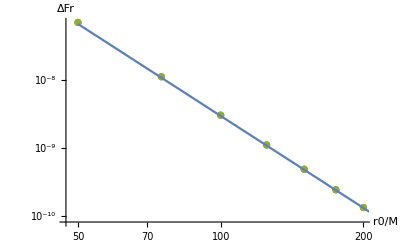

```mathematica
diff1=(Frap005-Fram005)/0.1
diff2=(Frap005-Frschw)/0.05
diff3=(Frschw-Fram005)/0.05

fig1=ListLogLogPlot[{Transpose@{rvals,Abs[diff1]},Transpose@{rvals,Abs[diff2]},Transpose@{rvals,Abs[diff3]}},AxesLabel->{r0/M,ΔFr}];
fig2=LogLogPlot[3*x^(-4.5),{x,50,250}];
Show[fig1,fig2]
```

## Timing test

```mathematica
fr = Timing[computeFrKerr[0,20.`70]]
```

Computing l=

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0``-3.81268889796175) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0``-3.9332543324997404 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Computing b, l=

Compute leading order

Compute subdominant order

Compute subsubdominant order

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

General::stop: Further output of Fit::fitm will be suppressed during this calculation.

{1683.,{Frinf→Indeterminate,Frh→Indeterminate,jump→Indeterminate,absoluteErrorFiniteSphericalSum→Indeterminate,absoluteErrorFiniteLSum→Indeterminate,dataRegH→{-0.000011551861856138759123690411497602820769856234609714807735,1.18062399076293670588161310116029255860016281133605671205×10^-6,4.53204359298703849512070021302035954699796210041053157617×10^-7,1.4282518758573894222050761953218244255442160584826×10^-7,5.39874616048431727149754239437059824932673786226657154×10^-8,2.48127441066883939432463547554894040280299×10^-8,1.3141123229313876801505185350899869210515366435554061×10^-8,7.66639627008086179992666293976311146×10^-9,4.792105215164898034087941785381852749375712302178043×10^-9,3.1558453451966686492781184501×10^-9,2.16560608104139076351151012369580862074984766253764×10^-9,1.536667966334993212472×10^-9,1.1211645718748025005806792867733713571857100620272×10^-9,8.375044396173868×10^-10,6.38382981738917210131274004670178956057048748458×10^-10,4.952156×10^-10,3.9010993887181824756749292599432326081732006509×10^-10,3.1×10^-10,2.517949751420299673212654399421669429880592472×10^-10,Indeterminate},dataRegI→{-0.000011551861856138759123690411497602820769856234609714807735,1.18062399076293670588161310116029255860016281133605671205×10^-6,4.53204359298703849512070021302035954699796210041053157617×10^-7,1.4282518758573894222050761953218244255442160584826×10^-7,5.39874616048431727149754239437059824932673786226657154×10^-8,2.48127441066883939432463547554894040280299×10^-8,1.3141123229313876801505185350899869210515366435554061×10^-8,7.66639627008086179992666293976311146×10^-9,4.792105215164898034087941785381852749375712302178043×10^-9,3.1558453451966686492781184501×10^-9,2.16560608104139076351151012369580862074984766253764×10^-9,1.536667966334993212472×10^-9,1.1211645718748025005806792867733713571857100620272×10^-9,8.375044396173868×10^-10,6.38382981738917210131274004670178956057048748458×10^-10,4.952156×10^-10,3.9010993887181824756749292599432326081732006509×10^-10,3.1×10^-10,2.517949751420299673212654399421669429880592472×10^-10,Indeterminate},dataH→{-0.002565762121140623954058524814085188340898760960287868844365,-0.00512970343525287789083194477895082514695752166974920877526412,-0.007694030297769406791622672774386507732081237167294435579896565,-0.0102562761107440273925974057935121013843664374213594836,-0.0128178066652924957061881246628483926233010641496624757096318,-0.0153790764128774952639470538284873824394176733924,-0.017940230774478688333687475535895294479682001956135419807453,-0.0205013254404419548791436580584103640384682,-0.023062385746397477210468438119981402973923269245708437608657,-0.0256234247513697827409161231369966557,-0.02818444980541645080843345665830793184953677841585688755229,-0.030745465323174549012358407288,-0.0333064740935863457152216119074364019882151282872694720354,-0.035867477951860858832726,-0.038428478147082542394870929646619530109267373237473949953,-0.040989475553987125,-0.04355047080030561442397302313264019720390166656360071086,-0.046111464346,-0.04867245653517757232688583895504735850466509117734187045,Indeterminate},dataIng→{0.0051171915932701154709433704207171392901402432469808511623083,0.007675219422098354484171213945719720904774152009031991235857759,0.01023286170252231853338174944015225674034310598299924443567406,0.01279258503248819088240827991089488150875057520044667644,0.0153530236208802155188188245314268086905086179436561643148363,0.0179137230162357089110611588556560372950846781725,0.0204745377975750087913220006381163436755130190802081802259122,0.0230354122745522351958670816054694925374195,0.025596321111537205814543565033766672022657090733660122433606,0.0281572512495053932340971435066196377,0.03071819533839921811658107347517657998842892050653663249887,0.0332791489635816128626573863349,0.0358401093361103091097954452057845466911359095781490080246,0.038401074620776288942293,0.040962043568495098330148654446337855411469003570969490116,0.043523015304531008,0.04608398920115301220104908794005362515822004918786768922,0.048644964798,0.05120594175216204019813879909738290069884196351715148964,Indeterminate}}}

```mathematica
fr[[2]]
```

{Frinf→0.00013624717088809442282186057847275719665,Frh→0.00013624717088809442282186057847275719665,jump→0.,absoluteErrorFiniteSphericalSum→7.66639627008086179992666293976311146×10^-9,absoluteErrorFiniteLSum→0.,dataRegH→{-0.000011551861856138759123690411497602820769856234609714807735,1.18062399076293670588161310116029255860016281133605671205×10^-6,4.53204359298703849512070021302035954699796210041053157617×10^-7,1.4282518758573894222050761953218244255442160584826×10^-7,5.39874616048431727149754239437059824932673786226657154×10^-8,2.48127441066883939432463547554894040280299×10^-8,1.3141123229313876801505185350899869210515366435554061×10^-8,7.66639627008086179992666293976311146×10^-9},dataRegI→{-0.000011551861856138759123690411497602820769856234609714807735,1.18062399076293670588161310116029255860016281133605671205×10^-6,4.53204359298703849512070021302035954699796210041053157617×10^-7,1.4282518758573894222050761953218244255442160584826×10^-7,5.39874616048431727149754239437059824932673786226657154×10^-8,2.48127441066883939432463547554894040280299×10^-8,1.3141123229313876801505185350899869210515366435554061×10^-8,7.66639627008086179992666293976311146×10^-9},dataH→{-0.002565762121140623954058524814085188340898760960287868844365,-0.00512970343525287789083194477895082514695752166974920877526412,-0.007694030297769406791622672774386507732081237167294435579896565,-0.0102562761107440273925974057935121013843664374213594836,-0.0128178066652924957061881246628483926233010641496624757096318,-0.0153790764128774952639470538284873824394176733924,-0.017940230774478688333687475535895294479682001956135419807453,-0.0205013254404419548791436580584103640384682},dataIng→{0.0051171915932701154709433704207171392901402432469808511623083,0.007675219422098354484171213945719720904774152009031991235857759,0.01023286170252231853338174944015225674034310598299924443567406,0.01279258503248819088240827991089488150875057520044667644,0.0153530236208802155188188245314268086905086179436561643148363,0.0179137230162357089110611588556560372950846781725,0.0204745377975750087913220006381163436755130190802081802259122,0.0230354122745522351958670816054694925374195}}

```mathematica
Export["C:\\Users\\SMP22EJG\\Documents\\GitHub\\ConservativeSelfForce\\Notebooks\\TheoData\\dataH.csv",dataH/.fr[[2]]]
Export["C:\\Users\\SMP22EJG\\Documents\\GitHub\\ConservativeSelfForce\\Notebooks\\TheoData\\dataI.csv",dataIng/.fr[[2]]]
Export["C:\\Users\\SMP22EJG\\Documents\\GitHub\\ConservativeSelfForce\\Notebooks\\TheoData\\dataRegH.csv",dataRegH/.fr[[2]]]
Export["C:\\Users\\SMP22EJG\\Documents\\GitHub\\ConservativeSelfForce\\Notebooks\\TheoData\\dataRegI.csv",dataRegI/.fr[[2]]]
```

C:\Users\SMP22EJG\Documents\GitHub\ConservativeSelfForce\Notebooks\TheoData\dataH.csv

C:\Users\SMP22EJG\Documents\GitHub\ConservativeSelfForce\Notebooks\TheoData\dataI.csv

C:\Users\SMP22EJG\Documents\GitHub\ConservativeSelfForce\Notebooks\TheoData\dataRegH.csv

C:\Users\SMP22EJG\Documents\GitHub\ConservativeSelfForce\Notebooks\TheoData\dataRegI.csv

```mathematica
Length[dataH/.fr[[2]]]
```

8

```mathematica
()[[1]]
```

Computing b, l=

Computing b, l=

Computing b, l=

«93 more identical outputs»

$Aborted

```mathematica
fr = Timing[computeFrKerr[7/10,10.`50]]
```

Computing l=

Computing b, l=

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Compute leading order

Compute subdominant order

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,1},{2,-1},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{0,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

Compute subsubdominant order

{686.878,{Frinf→0.001126431860910659317,Frh→0.001126431860967007373,jump→5.0023494×10^-11,absoluteErrorFiniteSphericalSum→1.579482699711×10^-7,absoluteErrorFiniteLSum→3.3219985721×10^-13}}

11.448